# Axions in Neutron Stars

```mathematica
Quit[]
```

### Globals

```mathematica
Msun=1.989*10^30;(* kg *)
GN = 6.67*10^-11; (* SI *)
G=(*6.70883*10^(-57)*)1; (* eV^-2 *)
clight = 2.99792*10^8; (* m/s *)
eV2joules=1.60218*10^(-19);
GeV2joules=1.60218*10^(-10);
mN = 0.939563; (* GeV *)
hbarGeV=6.582119569*10^(-25); (* GeV S *)
(*GNeV = 6.70883*10^(-39);*)
σN = 0.059;(* GeV *)(* eV*s *)
rkm=10^3 / (hbarGeV*clight);
rm=1/(hbarGeV*clight);

MeVperfm3 2 Jperm3=(10^-3*GeV2joules) * (10^(-15))^(-3);
Jperm3 2 m2 = GN / clight^4;
```

```mathematica
TOV replacements={div0Sols[[1]][[1]],λ'[r]->-Exp[λ[r]]*(2*G*M[r]/r^2 - 8*Pi*G*r*ρ[r]),Exp[λ[r]]->1/(1 - 2*G*M[r]/r),Exp[-λ[r]]->(1 - 2*G*M[r]/r),λ[r]->Log[1/(1 - 2*G*M[r]/r)],Derivative[1][p][r]->-(((M[r]+4*Pi*r^3*p[r])*(p[r]+ρ[r]))/(r*(r-2*M[r])))};
```

Part::partd: Part specification div0Sols⟦1⟧ is longer than depth of object.

```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts,xcolor}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{color,txfonts,xcolor}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
c1=RGBColor[101/255,144/255,255/255];
c2=RGBColor[121/255,94/255,240/255];
c3=RGBColor[221/255,38/255,129/255];
c4=RGBColor[255/255,97/255,2/255];
c5=RGBColor[254/255,176/255,1/255];
c6=RGBColor[200/255,200/255,200/255];
```

### checking unit conversions

```mathematica
GeV2joules/ ((hbarGeV*clight)^3)
```

2.08523×10^37

# Derive TOV Equation

## Linearized

### Set up relevant tensors

```mathematica
coord = {t, r, θ, ϕ};
dim = 4;
metric = DiagonalMatrix[{Exp[ν[r]+ (ζ[r]+Δ[r])*ϵ*r^2],-Exp[λ[r]+(ζ[r]-Δ[r])*ϵ*r^2] ,-r^2,-r^2*Sin[θ]^2}];
```

```mathematica
SetDirectory["/Users/wentmich/Documents/uiuc/classes/physics_598-AdS:CFT/"]
<<diffgeo.m
```

/Users/wentmich/Documents/uiuc/classes/physics_598-AdS:CFT

```mathematica
metric bar = Normal[Series[metric,{ϵ,0,0}]];
inverse bar = Inverse[metric bar];
Einstein linear = Simplify[Normal[Series[Einstein,{ϵ,0,1}]]/.{ϵ->1}];
Einstein bar = Simplify[Einstein/.{ϵ->0}];
```

```mathematica
Einstein bar
```

((ⅇ^(ν(r)-λ(r)) (r λ'(r)+ⅇ^(λ(r))-1))/r^2 | 0 | 0 | 0
0 | (-ⅇ^(λ(r))+r ν'(r)+1)/r^2 | 0 | 0
0 | 0 | 1/4 r ⅇ^(-λ(r)) (-λ'(r) (r ν'(r)+2)+2 r ν''(r)+r (ν'(r))^2+2 ν'(r)) | 0
0 | 0 | 0 | 1/4 r sin^2(θ) ⅇ^(-λ(r)) (-λ'(r) (r ν'(r)+2)+2 r ν''(r)+r (ν'(r))^2+2 ν'(r)))

```mathematica
Einstein linear
```

```mathematica
metric bar
```

(ⅇ^(ν(r)) | 0 | 0 | 0
0 | -ⅇ^(λ(r)) | 0 | 0
0 | 0 | -r^2 | 0
0 | 0 | 0 | -r^2 sin^2(θ))

```mathematica
TNSud=zeroTensor[2];
TNSud[[t,t]]=ρ[r];
TNSud[[r,r]]=TNSud[[θ,θ]]=TNSud[[ϕ,ϕ]]=-p[r];
```

```mathematica
metric bar*TNSud
```

(ⅇ^(ν(r)) ρ(r) | 0 | 0 | 0
0 | p(r) ⅇ^(λ(r)) | 0 | 0
0 | 0 | r^2 p(r) | 0
0 | 0 | 0 | r^2 sin^2(θ) p(r))

```mathematica
V[r]=-b*(ϵ-d*ρ[r])*Abs[Cos[a[r]/(2*fa)]];
dVdr[r]=Simplify[D[V[r],r]];
dVda[r]=D[V[r],a[r]];
Taud=zeroTensor[2];
Taud[[t,t]]=Taud[[r,r]]=Taud[[θ,θ]]=Taud[[ϕ,ϕ]]=Simplify[(1/2)*((-Exp[-λ[r]])*(a'[r])^2+2*Va[r])];
Taud[[r,r]]=Simplify[Taud[[r,r]]+Exp[-λ[r]]*(a'[r])^2];
```

```mathematica
Ttud = TNSud+Taud;
```

```mathematica
TNSdd=metric bar*TNSud;
Tadd=metric bar*Taud;
Ttdd=metric bar*Ttud;
```

```mathematica
Ttdd
```

(ⅇ^(ν(r)) (-1/2 ⅇ^(-λ(r)) (a'(r))^2+ρ(r)+Va(r)) | 0 | 0 | 0
0 | -ⅇ^(λ(r)) (1/2 ⅇ^(-λ(r)) (a'(r))^2-p(r)+Va(r)) | 0 | 0
0 | 0 | -r^2 (-1/2 ⅇ^(-λ(r)) (a'(r))^2-p(r)+Va(r)) | 0
0 | 0 | 0 | -r^2 sin^2(θ) (-1/2 ⅇ^(-λ(r)) (a'(r))^2-p(r)+Va(r)))

### Solve Standard TOV

```mathematica
eq1=Einstein bar[[1,1]]==8*Pi*G*TNSdd[[1,1]]//Simplify
```

8 π r ⅇ^(λ(r)) ρ(r)==(r λ'(r)+ⅇ^(λ(r))-1)/r

Integrating from 0 → r gives us exp(λ(r)) = 1 / (1 - 2M(r)/r) since the metric must be asymptotically flat. M(r) is the mass enclosed within r. True even when ρ and p are functions of r.

```mathematica
eq1/.{Exp[λ[r]]->1/(1 - 2*G*M[r]/r),Exp[-λ[r]]->(1-2*G*M[r]/r)}//Simplify
```

(8 π r^2 ρ(r))/(r-2 M(r))==(2 M(r))/(r^2-2 r M(r))+λ'(r)

```mathematica
eq2=Einstein bar[[2,2]]==8*Pi*G*TNSdd[[2,2]]/.{Exp[λ[r]]->1/(1 - 2*G*M[r]/r),Exp[-λ[r]]->(1-2*G*M[r]/r)}//Simplify
(*eq1=Einstein[[3,3]]==8*Pi*TNSdd[[3,3]](*/.{Exp[λ[r]]->1/(2*M[r]/r+1),Exp[-λ[r]]->(2*M[r]/r+1)}*)//Simplify*)
```

(r ν'(r)-(2 M(r))/(r-2 M(r)))/r^2==(8 π r p(r))/(r-2 M(r))

```mathematica
%//TeXForm
```

\frac{r \nu '(r)-\frac{2 M(r)}{r-2 M(r)}}{r^2}=\frac{8 \pi  r p(r)}{r-2 M(r)}

```mathematica
(* enforce that TNS is divergence free *)
divTNSud =covariant[TNSud,{up,down}]/.{ϵ->0};
divTNSud = Table[Simplify[Sum[divTNSud[[i,i,k]],{i,1,4}]],{k,1,4}]
```

{0,-p'(r)-1/2 (p(r)+ρ(r)) ν'(r),0,0}

```mathematica
%[[2]]//TeXForm
```

-p'(r)-\frac{1}{2} (p(r)+\rho (r)) \nu '(r)

```mathematica
div0Sols=Solve[divTNSud[[2]]==0,ν'[r]]
```

{{ν'(r)→-(2 p'(r))/(p(r)+ρ(r))}}

```mathematica
eq2= eq2/.div0Sols[[1]]
```

(-(2 M(r))/(r-2 M(r))-(2 r p'(r))/(p(r)+ρ(r)))/r^2==(8 π r p(r))/(r-2 M(r))

```mathematica
dpdr TOV = Solve[eq2,p'[r]][[1]]
```

{p'(r)→-((M(r)+4 π r^3 p(r)) (p(r)+ρ(r)))/(r (r-2 M(r)))}

```mathematica
p'[r]/.dpdr TOV
```

-((M(r)+4 π r^3 p(r)) (p(r)+ρ(r)))/(r (r-2 M(r)))

```mathematica
eq1
```

8 π r ⅇ^(λ(r)) ρ(r)==(r λ'(r)+ⅇ^(λ(r))-1)/r

```mathematica
ν'[r]//.TOV replacements
```

ν'(r)//.{{{ν'(r)→-(2 p'(r))/(p(r)+ρ(r))}},λ'(r)→-ⅇ^(λ(r)) ((2 M(r))/r^2-8 π r ρ(r)),ⅇ^(λ(r))→1/(1-(2 M(r))/r),ⅇ^(-λ(r))→1-(2 M(r))/r,λ(r)→log(1/(1-(2 M(r))/r)),p'(r)→-((M(r)+4 π r^3 p(r)) (p(r)+ρ(r)))/(r (r-2 M(r)))}

```mathematica
eq1/.{Exp[λ[r]]->1/(1 - 2*G*M[r]/r),Exp[-λ[r]]->(1-2*G*M[r]/r)}//.dpdr TOV//.TOV replacements//Simplify
eq2/.{Exp[λ[r]]->1/(1 - 2*G*M[r]/r),Exp[-λ[r]]->(1-2*G*M[r]/r)}/.dpdr TOV//Simplify
```

(8 π r^2 ρ(r))/(r-2 M(r))==(2 M(r))/(r^2-2 r M(r))+λ'(r)//.{{{ν'(r)→-(2 p'(r))/(p(r)+ρ(r))}},λ'(r)→ⅇ^(λ(r)) (8 π r ρ(r)-(2 M(r))/r^2),ⅇ^(λ(r))→r/(r-2 M(r)),ⅇ^(-λ(r))→1-(2 M(r))/r,λ(r)→log(r/(r-2 M(r))),p'(r)→-((M(r)+4 π r^3 p(r)) (p(r)+ρ(r)))/(r (r-2 M(r)))}

True

```mathematica
%//TeXForm
```

\text{True}

This is the solution to the NS background. In the next part, we’ll look at the linearized versions of everything.

### Solve for ζ and Δ

```mathematica
eq11=Einstein linear[[1,1]]==8*Pi*G*Ttdd[[1,1]]//Simplify
eq22=Einstein linear[[2,2]]==8*Pi*G*Ttdd[[2,2]]//Simplify
```

r^2 Δ'(r)+8 π r ⅇ^(λ(r)) ρ(r)+8 π r ⅇ^(λ(r)) Va(r)+1/r==4 π r (a'(r))^2+r^2 ζ'(r)+r Δ(r) (2 r λ'(r)+ⅇ^(λ(r))-4)+r ζ(r) (ⅇ^(λ(r))+2)+λ'(r)+ⅇ^(λ(r))/r

4 π (a'(r))^2+(-ⅇ^(λ(r))+r ν'(r)+1)/r^2+r Δ'(r)+Δ(r) ⅇ^(λ(r))+2 Δ(r)+r ζ'(r)+2 ζ(r)+8 π ⅇ^(λ(r)) Va(r)==ⅇ^(λ(r)) (8 π p(r)+ζ(r))

```mathematica
perturbation replacements = FullSimplify[Solve[eq11&&eq22,{ζ'[r],Δ'[r]}][[1]]/.div0Sols[[1]]/.{λ'[r]->-Exp[λ[r]]*(2*G*M[r]/r^2 - 8*Pi*G*r*ρ[r])}/.{Exp[λ[r]]->1/(1 - 2*G*M[r]/r),Exp[-λ[r]]->(1 - 2*G*M[r]/r)}/.{λ[r]->Log[1/(1 - 2*G*M[r]/r)]}//FullSimplify]
```

{ζ'(r)→((M(r) (4 r^2 (2 π (a'(r))^2+ζ(r))+1)-2 r^3 (2 π ((a'(r))^2-p(r)+2 r^2 Δ(r) ρ(r))+ζ(r)))/(r-2 M(r))+(r p'(r))/(p(r)+ρ(r)))/r^3,Δ'(r)→((M(r) (4 r^2 Δ(r)+1)+r^3 (4 π (p(r)+2 r^2 Δ(r) ρ(r)-2 Va(r))-3 Δ(r)+ζ(r)))/(r-2 M(r))+(r p'(r))/(p(r)+ρ(r)))/r^3}

```mathematica
perturbation replacements=perturbation replacements/.dpdr TOV//FullSimplify
```

{ζ'(r)→(2 (-2 π (a'(r))^2-(4 π r^3 Δ(r) ρ(r))/(r-2 M(r))-ζ(r)))/r,Δ'(r)→(Δ(r) (4 M(r)+8 π r^3 ρ(r)-3 r)+r ζ(r)-8 π r Va(r))/(r (r-2 M(r)))}

```mathematica
Δcoef = Coefficient[Expand[Δ'[r]/.perturbation replacements],Δ[r]]//FullSimplify
ζcoef = Coefficient[Expand[Δ'[r]/.perturbation replacements],ζ[r]]//FullSimplify
affine=FullSimplify[Expand[Δ'[r]/.perturbation replacements]-Δcoef*Δ[r]-ζcoef*ζ[r]]
```

(4 M(r)+8 π r^3 ρ(r)-3 r)/(r (r-2 M(r)))

1/(r-2 M(r))

-(8 π Va(r))/(r-2 M(r))

```mathematica
Δcoef = Coefficient[Expand[ζ'[r]/.perturbation replacements],Δ[r]]//FullSimplify
ζcoef = Coefficient[Expand[ζ'[r]/.perturbation replacements],ζ[r]]//FullSimplify
affine=FullSimplify[Expand[ζ'[r]/.perturbation replacements]-Δcoef*Δ[r]-ζcoef*ζ[r]]
```

-(8 π r^2 ρ(r))/(r-2 M(r))

-2/r

-(4 π (a'(r))^2)/r

We want to check whether the total stress energy is conserved to linear order given this expressions for λ, ν, ζ, and Δ.

Do we need to expand these in powers of a as well? I think lowest order should be a^2.

First, just sub in all the things we know.

```mathematica
div0Sols[[1]]
```

{ν'(r)→-(2 p'(r))/(p(r)+ρ(r))}

```mathematica
perturbation replacements=perturbation replacements/.div0Sols[[1]]/.{λ'[r]->Exp[λ[r]]*(2*G*M[r]/r^2 - 8*Pi*G*r*ρ[r])}/.{Exp[λ[r]]->-1/(2*G*M[r]/r-1),Exp[-λ[r]]->-(2*G*M[r]/r-1)}/.{λ[r]->Log[-1/(2*G*M[r]/r-1)]}//FullSimplify
```

{ζ'(r)→(2 (-2 π (a'(r))^2-(4 π r^3 Δ(r) ρ(r))/(r-2 M(r))-ζ(r)))/r,Δ'(r)→(Δ(r) (4 M(r)+8 π r^3 ρ(r)-3 r)+r ζ(r)-8 π r Va(r))/(r (r-2 M(r)))}

```mathematica
perturbation replacements=perturbation replacements/.dpdr TOV//FullSimplify
```

{ζ'(r)→(2 (-2 π (a'(r))^2-(4 π r^3 Δ(r) ρ(r))/(r-2 M(r))-ζ(r)))/r,Δ'(r)→(Δ(r) (4 M(r)+8 π r^3 ρ(r)-3 r)+r ζ(r)-8 π r Va(r))/(r (r-2 M(r)))}

There’s still a ν in there. Did I make a mistake with the metric indices? How can I get this ν in terms of p and ρ? Changing the definitions of the perturbations works. Ah fudge, I wasn’t accounting for the fact that there are derivatives of ζ and Δ in the covariant derivative. That massively complicates things because now we have to solve a differential equation for each of these.

```mathematica
D[Exp[λ[r]]/.{Exp[λ[r]]->-1/(2*G*M[r]/r-1),Exp[-λ[r]]->-(2*G*M[r]/r-1)}, r]//Simplify
```

(2 (r M'(r)-M(r)))/(r-2 M(r))^2

### Check divergence

```mathematica
divTtotαμν = covariant[Ttud,{up, down}];
divTtotμμν = Table[Simplify[Sum[divTtotαμν[[i,i,k]],{i,1,4}]],{k,1,4}]
```

{0,(ⅇ^(-λ(r)) ((a'(r))^2 (-r λ'(r)+r ν'(r)+r ϵ ζ'(r)+4)+2 r a'(r) a''(r)-r ⅇ^(λ(r)) (2 p'(r)+(p(r)+ρ(r)) (ν'(r)+ϵ ζ'(r))-2 Va'(r))))/(2 r),0,0}

```mathematica
divTtotμμr linear = Simplify[Normal[Series[divTtotμμν[[2]],{ϵ,0,1}]]/.{ϵ->1}]
```

(ⅇ^(-λ(r)) ((a'(r))^2 (r ζ'(r)-r λ'(r)+r ν'(r)+4)+2 r a'(r) a''(r)-r ⅇ^(λ(r)) (2 p'(r)+(p(r)+ρ(r)) (ζ'(r)+ν'(r))-2 Va'(r))))/(2 r)

```mathematica
divTtotμμr linear replaced = Simplify[divTtotμμr linear/.perturbation replacements/.dpdr TOV]
```

1/(2 r)ⅇ^(-λ(r)) (-r ⅇ^(λ(r)) ((p(r)+ρ(r)) (-4 π r (a'(r))^2+(Δ(r)-8 π r^2 Va(r))/(r-2 M(r))+ν'(r))-(2 (M(r)+4 π r^3 p(r)) (p(r)+ρ(r)))/(r (r-2 M(r)))-2 Va'(r))+(a'(r))^2 (r ((Δ(r)-8 π r^2 Va(r))/(r-2 M(r))-4 π r (a'(r))^2)-r λ'(r)+r ν'(r)+4)+2 r a'(r) a''(r))

We still run into the same problem as before where the EOMs need to be applied and dVdr ≠ dVda * dadr. Let’s throw in the potential just to see what happens though.

```mathematica
axion EOM replacement = {a''[r]->(1/inverse bar[[2,2]])*(dVda[r])}; (* sign on the RHS correct? *)
```

```mathematica
divTtotμμr linear replaced =divTtotμμr linear replaced/.{Va'[r]->dVdr[r], Va[r]->V[r]}/.axion EOM replacement;
```

```mathematica
divTtotμμr linear replaced =Simplify[divTtotμμr linear replaced ];
```

```mathematica
divTtotμμr linear replaced =divTtotμμr linear replaced /.div0Sols[[1]];
```

```mathematica
divTtotμμr linear replaced =Simplify[divTtotμμr linear replaced ];
```

```mathematica
divTtotμμr linear replaced =divTtotμμr linear replaced /.dpdr TOV;
```

```mathematica
divTtotμμr linear replaced =Simplify[divTtotμμr linear replaced]
```

1/(2 r (r-2 M(r)))(ⅇ^(-λ(r)) (a'(r))^2 (2 M(r) (4 π r^2 (a'(r))^2+r λ'(r)-3)+r (-4 π r^2 (a'(r))^2+8 π r^2 p(r)+Δ(r)-r λ'(r)+4)+8 π b r^3 (ϵ-d ρ(r)) Abs[cos((a(r))/(2 fa))])-(p(r)+ρ(r)) (-4 π r^2 (r-2 M(r)) (a'(r))^2+8 π b r^3 (ϵ-d ρ(r)) Abs[cos((a(r))/(2 fa))]+2 (M(r)+4 π r^3 p(r))+r Δ(r))+2 b d r (r-2 M(r)) ρ'(r) Abs[cos((a(r))/(2 fa))]+2 (M(r)+4 π r^3 p(r)) (p(r)+ρ(r)))

We can also sub in λ and λ’.

```mathematica
λ replacement = {λ[r]->Log[-1/(2*M[r]/r-1)]};
λprime replacement = {λ'[r]->Simplify[D[Log[-1/(2*M[r]/r-1)],r]]};
mprime replacement = {M'[r]->4*Pi*r^2*ρ[r]};
```

```mathematica
divTtotμμr linear replaced =divTtotμμr linear replaced /.λprime replacement;
divTtotμμr linear replaced =divTtotμμr linear replaced /.λ replacement;
divTtotμμr linear replaced =divTtotμμr linear replaced /.mprime replacement;
```

```mathematica
divTtotμμr linear replaced =Simplify[divTtotμμr linear replaced]
```

-((a'(r))^2 (M(r) (4-8 π r^2 (a'(r))^2)-r (-4 π r^2 (a'(r))^2+8 π r^2 p(r)-8 π r^2 ρ(r)+Δ(r)+4)-8 π b r^3 (ϵ-d ρ(r)) Abs[cos((a(r))/(2 fa))]))/(2 r^2)-((p(r)+ρ(r)) (-4 π r^2 (r-2 M(r)) (a'(r))^2+8 π b r^3 (ϵ-d ρ(r)) Abs[cos((a(r))/(2 fa))]+2 (M(r)+4 π r^3 p(r))+r Δ(r)))/(2 r (r-2 M(r)))+b d ρ'(r) Abs[cos((a(r))/(2 fa))]+((M(r)+4 π r^3 p(r)) (p(r)+ρ(r)))/(r (r-2 M(r)))

Is this setting a condition on anything? ρ and p are already fixed. M is therefore fixed. a comes from EOM. It can’t fix anything, but we should check that it’s true after solving for a(r).

Am I able to solve for a’(r) by integrating EOM? No, can’t split potential. Just needs to be checked after solving for axion field.

Actually, we get a ρ’(r) in here. Where is that coming from and can we get rid of it?

```mathematica
FullSimplify[Solve[divTtotμμr linear replaced==0,ρ'[r]][[1]]]
```

{ρ'(r)→1/(2 b d r^2 (r-2 M(r)) Abs[cos((a(r))/(2 fa))])(8 π b r^3 (ϵ-d ρ(r)) Abs[cos((a(r))/(2 fa))] (r (p(r)+ρ(r))-(r-2 M(r)) (a'(r))^2)-(r-2 M(r)) (a'(r))^2 (r (4 π r^2 (3 p(r)-ρ(r))+Δ(r)+4)-4 M(r))+4 π r^2 (r-2 M(r))^2 (a'(r))^4+r^2 Δ(r) (p(r)+ρ(r)))}

Is this an extra condition? I don’t think so. I believe it should be satisfied automatically since a’(r) should be dependent on ρ’(r) in some way. Basically, the axion should affect the NS parameters.

## Complete (nothing here)

### Set up relevant tensors

```mathematica
coord = {t, r, θ, ϕ};
dim = 4;
metric = DiagonalMatrix[{Exp[ν[r]+ ζ[r]] (*+ ζ[r]*ϵ*),-Exp[λ[r]+ Δ[r]] (*- Δ[r]*ϵ*),-r^2,-r^2*Sin[θ]^2}];
```

```mathematica
SetDirectory["/Users/wentmich/Documents/uiuc/classes/physics_598-AdS:CFT/"]
<<diffgeo.m
```

/Users/wentmich/Documents/uiuc/classes/physics_598-AdS:CFT

```mathematica
TNSud=zeroTensor[2];
TNSud[[t,t]]=ρ[r];
TNSud[[r,r]]=TNSud[[θ,θ]]=TNSud[[ϕ,ϕ]]=-p[r];
```

```mathematica
V[r]=-b*(ϵ-d*ρ[r])*Abs[Cos[a[r]/(2*fa)]];
dVdr[r]=Simplify[D[V[r],r]];
dVda[r]=D[V[r],a[r]];
Taud=zeroTensor[2];
Taud[[t,t]]=Taud[[r,r]]=Taud[[θ,θ]]=Taud[[ϕ,ϕ]]=Simplify[(1/2)*((-Exp[-λ[r]-Δ[r]])*(a'[r])^2+2*Va[r])];
Taud[[r,r]]=Simplify[Taud[[r,r]]+Exp[-λ[r]]*(a'[r])^2];
```

```mathematica
Ttud = TNSud+Taud;
```

```mathematica
TNSdd=metric.TNSud;
Tadd=metric.Taud;
Ttdd=metric.Ttud;
```

```mathematica
Ttud
```

(-1/2 (a'(r))^2 ⅇ^(-Δ(r)-λ(r))+ρ(r)+Va(r) | 0 | 0 | 0
0 | 1/2 (2 ⅇ^(Δ(r))-1) (a'(r))^2 ⅇ^(-Δ(r)-λ(r))-p(r)+Va(r) | 0 | 0
0 | 0 | -1/2 (a'(r))^2 ⅇ^(-Δ(r)-λ(r))-p(r)+Va(r) | 0
0 | 0 | 0 | -1/2 (a'(r))^2 ⅇ^(-Δ(r)-λ(r))-p(r)+Va(r))

### Solve Standard TOV

```mathematica
eq1=Einstein bar[[1,1]]==8*Pi*TNSdd[[1,1]]//Simplify
```

8 π r ⅇ^(λ(r)) ρ(r)==(r λ'(r)+ⅇ^(λ(r))-1)/r

```mathematica
DSolve[eq1,λ[r],r]
```

Solve[(ⅇ^(-λ(r)) (-1+ⅇ^(λ(r)))-8 π K[1]^2 ρ(K[1]))K[1]1r+-ⅇ^(-K[2]) (ⅇ^K[2] (1-ⅇ^(-K[2]) (-1+ⅇ^K[2]))K[1]1r-r)K[2]1λ(r)==1,λ(r)]

Integrating from 0 → r gives us exp(λ(r)) = 1 / (1 + 2M(r)/r) since the metric must be asymptotically flat. M(r) is the mass enclosed within r. True even when ρ and p are functions of r.

```mathematica
eq1=Einstein bar[[2,2]]==8*Pi*TNSdd[[2,2]]/.{Exp[λ[r]]->-1/(2*M[r]/r-1),Exp[-λ[r]]->-(2*M[r]/r-1)}//Simplify
(*eq1=Einstein[[3,3]]==8*Pi*TNSdd[[3,3]](*/.{Exp[λ[r]]->1/(2*M[r]/r+1),Exp[-λ[r]]->(2*M[r]/r+1)}*)//Simplify*)
```

(r ν'(r)-(2 M(r))/(r-2 M(r)))/r^2==(8 π r p(r))/(r-2 M(r))

```mathematica
%//TeXForm
```

\frac{r \nu '(r)-\frac{2 M(r)}{r-2 M(r)}}{r^2}=\frac{8 \pi  r p(r)}{r-2 M(r)}

```mathematica
(* enforce that TNS is divergence free *)
divTNSud =covariant[TNSud,{up,down}]/.{ϵ->0};
divTNSud = Table[Simplify[Sum[divTNSud[[i,i,k]],{i,1,4}]],{k,1,4}]
```

{0,-p'(r)-1/2 (p(r)+ρ(r)) ν'(r),0,0}

```mathematica
%[[2]]//TeXForm
```

-p'(r)-\frac{1}{2} (p(r)+\rho (r)) \nu '(r)

```mathematica
div0Sols=Solve[divTNSud[[2]]==0,ν'[r]]
```

{{ν'(r)→-(2 p'(r))/(p(r)+ρ(r))}}

```mathematica
eq1 = eq1/.div0Sols[[1]]
```

(-(2 M(r))/(r-2 M(r))-(2 r p'(r))/(p(r)+ρ(r)))/r^2==(8 π r p(r))/(r-2 M(r))

```mathematica
dpdr TOV = Solve[eq1,p'[r]][[1]]
```

{p'(r)→-((M(r)+4 π r^3 p(r)) (p(r)+ρ(r)))/(r (r-2 M(r)))}

```mathematica
p'[r]/.dpdr TOV
```

-((M(r)+4 π r^3 p(r)) (p(r)+ρ(r)))/(r (r-2 M(r)))

```mathematica
%//TeXForm
```

-\frac{\left(M(r)+4 \pi  r^3 p(r)\right) (p(r)+\rho (r))}{r (r-2 M(r))}

This is the solution to the NS background. In the next part, we’ll look at the linearized versions of everything.

### Solve for ζ and Δ

```mathematica
eq11=Einstein linear[[1,1]]==8*Pi*Ttdd[[1,1]]//Simplify
eq22=Einstein linear[[2,2]]==8*Pi*Ttdd[[2,2]]//Simplify
```

(ⅇ^(ν(r)-λ(r)) (r Δ'(r)+Δ(r) (1-r λ'(r))+ζ(r) (r λ'(r)+ⅇ^(λ(r))-1)+r λ'(r)+ⅇ^(λ(r))-1))/r^2==8 π ⅇ^(ν(r)) (-1/2 ⅇ^(-λ(r)) (a'(r))^2+ρ(r)+Va(r))

4 π ((a'(r))^2-2 p(r) ⅇ^(λ(r))+2 ⅇ^(λ(r)) Va(r))+(Δ(r) (-ⅇ^(λ(r)))+r ζ'(r)-ⅇ^(λ(r))+r ν'(r)+1)/r^2==0

```mathematica
perturbation replacements = FullSimplify[Solve[eq11&&eq22,{ζ'[r],Δ'[r]}][[1]]/.div0Sols[[1]]/.{λ'[r]->Exp[λ[r]]*(2*M[r]/r^2 - 8*Pi*r*ρ[r])}/.{Exp[λ[r]]->-1/(2*M[r]/r-1),Exp[-λ[r]]->-(2*M[r]/r-1)}/.{λ[r]->Log[-1/(2*M[r]/r-1)]}//FullSimplify]
```

{ζ'(r)→-4 π r (a'(r))^2+(2 M(r)+8 π r^3 (p(r)-Va(r))+r Δ(r))/(r (r-2 M(r)))+(2 p'(r))/(p(r)+ρ(r)),Δ'(r)→(4 M(r) (2 π r^2 (a'(r))^2+Δ(r)-ζ(r)-1)-4 π r^3 ((a'(r))^2+2 ρ(r) (Δ(r)-ζ(r)))+16 π r^3 ρ(r)+8 π r^3 Va(r)-r Δ(r))/(r (r-2 M(r)))}

```mathematica
perturbation replacements=perturbation replacements/.dpdr TOV//FullSimplify
```

{ζ'(r)→(Δ(r)-8 π r^2 Va(r))/(r-2 M(r))-4 π r (a'(r))^2,Δ'(r)→(4 M(r) (2 π r^2 (a'(r))^2+Δ(r)-ζ(r)-1)-4 π r^3 ((a'(r))^2+2 ρ(r) (Δ(r)-ζ(r)))+16 π r^3 ρ(r)+8 π r^3 Va(r)-r Δ(r))/(r (r-2 M(r)))}

```mathematica
Δcoef = Coefficient[Expand[Δ'[r]/.perturbation replacements],Δ[r]]//FullSimplify
ζcoef = Coefficient[Expand[Δ'[r]/.perturbation replacements],ζ[r]]//FullSimplify
affine=FullSimplify[Expand[Δ'[r]/.perturbation replacements]-Δcoef*Δ[r]-ζcoef*ζ[r]]
```

-(-4 M(r)+8 π r^3 ρ(r)+r)/(r^2-2 r M(r))

(8 π r^3 ρ(r)-4 M(r))/(r (r-2 M(r)))

(8 π r^3 (2 ρ(r)+Va(r))-4 M(r))/(r (r-2 M(r)))-4 π r (a'(r))^2

We want to check whether the total stress energy is conserved to linear order given this expressions for λ, ν, ζ, and Δ.

Do we need to expand these in powers of a as well? I think lowest order should be a^2.

First, just sub in all the things we know.

```mathematica
div0Sols[[1]]
```

{ν'(r)→-(2 p'(r))/(p(r)+ρ(r))}

```mathematica
perturbation replacements=perturbation replacements/.div0Sols[[1]]/.{λ'[r]->Exp[λ[r]]*(2*M[r]/r^2 - 8*Pi*r*ρ[r])}/.{Exp[λ[r]]->-1/(2*M[r]/r-1),Exp[-λ[r]]->-(2*M[r]/r-1)}/.{λ[r]->Log[-1/(2*M[r]/r-1)]}//FullSimplify
```

{ζ(r)→1/(4 (r-2 M(r)) (M(r)-2 π r^3 ρ(r)))(1-(2 M(r))/r) (-(r-2 M(r)) (-4 M(r)+8 π r^3 ρ(r)+r) (r (4 π r (a'(r))^2-(2 p'(r))/(p(r)+ρ(r))+ζ'(r))+1)+r (r-2 M(r)) (-4 π r^2 (a'(r))^2+(2 (-4 M(r)+8 π r^3 ρ(r)+r) (4 π r^2 (p(r)-Va(r))+1))/(r-2 M(r))-r Δ'(r))+r^2 (8 π r^2 (ρ(r)+Va(r))-1)),Δ(r)→(1-(2 M(r))/r) (r (4 π r ((a'(r))^2+(2 r (Va(r)-p(r)))/(r-2 M(r)))-(2 p'(r))/(p(r)+ρ(r))+ζ'(r))-r/(r-2 M(r))+1)}

```mathematica
perturbation replacements=perturbation replacements/.dpdr TOV//FullSimplify
```

{ζ→-(2 π r (r-2 M(r)) (a'(r))^2 (-2 M(r)+4 π r^3 ρ(r)+r)-8 π r^2 M(r) Va(r)+M(r)+16 π^2 r^5 ρ(r) Va(r)-4 π r^3 ρ(r))/(M(r)-2 π r^3 ρ(r)),Δ→4 π r ((r-2 M(r)) (a'(r))^2+2 r Va(r))}

There’s still a ν in there. Did I make a mistake with the metric indices? How can I get this ν in terms of p and ρ? Changing the definitions of the perturbations works. Ah fudge, I wasn’t accounting for the fact that there are derivatives of ζ and Δ in the covariant derivative. That massively complicates things because now we have to solve a differential equation for each of these.

### Check divergence

```mathematica
divTtotαμν = covariant[Ttud,{up, down}];
divTtotμμν = Table[Simplify[Sum[divTtotαμν[[i,i,k]],{i,1,4}]],{k,1,4}]
```

{0,(ⅇ^(-λ(r)) ((a'(r))^2 (-r λ'(r)+r ν'(r)+4)+2 r a'(r) a''(r)-r ⅇ^(λ(r)) (2 p'(r)+(p(r)+ρ(r)) ν'(r)-2 Va'(r))))/(2 r),0,0}

```mathematica
divTtotμμr linear = Simplify[Normal[Series[divTtotμμν[[2]],{ϵ,0,1}]]/.{ϵ->1}]
```

(ⅇ^(-λ(r)) ((a'(r))^2 (-r λ'(r)+r ν'(r)+4)+2 r a'(r) a''(r)-r ⅇ^(λ(r)) (2 p'(r)+(p(r)+ρ(r)) ν'(r)-2 Va'(r))))/(2 r)

```mathematica
divTtotμμr linear replaced = Simplify[divTtotμμr linear/.perturbation replacements/.dpdr TOV]
```

1/2 ((ⅇ^(-λ(r)) ν'(r) (-(a'(r))^2+p(r) ⅇ^(λ(r))+ⅇ^(λ(r)) ρ(r)) (ⅇ^(λ(r)) (r (4 π r (-(a'(r))^2+4 r (Va(r)-p(r)) λ'(r)+2 p(r)-2 Va(r))-3 λ'(r))+2)+(2 r λ'(r)-1) (r (4 π r (a'(r))^2+ν'(r))+1)+ⅇ^(2 λ(r)) (8 π r^2 (ρ(r)+Va(r))-1)))/(r (2 r λ'(r)-1) ν'(r)+ⅇ^(λ(r)) (r λ'(r)-1)+ⅇ^(2 λ(r)))+ⅇ^(-λ(r)) (a'(r))^2 (-λ'(r)+ν'(r)+4/r)+2 ⅇ^(-λ(r)) a'(r) a''(r)+(2 (M(r)+4 π r^3 p(r)) (p(r)+ρ(r)))/(r (r-2 M(r)))-(p(r)+ρ(r)) ν'(r)+2 Va'(r))

We still run into the same problem as before where the EOMs need to be applied and dVdr ≠ dVda * dadr. Let’s throw in the potential just to see what happens though.

```mathematica
axion EOM replacement = {a''[r]->(1/inverse bar[[2,2]])*(dVda[r])}; (* sign on the RHS correct? *)
```

```mathematica
divTtotμμr linear replaced =divTtotμμr linear replaced/.{Va'[r]->dVdr[r], Va[r]->V[r]}/.axion EOM replacement;
```

```mathematica
divTtotμμr linear replaced =Simplify[divTtotμμr linear replaced ];
```

```mathematica
divTtotμμr linear replaced =divTtotμμr linear replaced /.div0Sols[[1]];
```

```mathematica
divTtotμμr linear replaced =Simplify[divTtotμμr linear replaced ];
```

```mathematica
divTtotμμr linear replaced =divTtotμμr linear replaced /.dpdr TOV;
```

```mathematica
divTtotμμr linear replaced =Simplify[divTtotμμr linear replaced]
```

(ⅇ^(-λ(r)) (M(r)+4 π r^3 p(r)) (-(a'(r))^2+p(r) ⅇ^(λ(r))+ⅇ^(λ(r)) ρ(r)) (ⅇ^(λ(r)) (r (4 π r (-(a'(r))^2-2 b (2 r λ'(r)-1) (ϵ-d ρ(r)) Abs[cos((a(r))/(2 fa))]+p(r) (2-4 r λ'(r)))-3 λ'(r))+2)+(2 r λ'(r)-1) (4 π r^2 (a'(r))^2+(2 (M(r)+4 π r^3 p(r)))/(r-2 M(r))+1)+ⅇ^(2 λ(r)) (8 π r^2 (ρ(r)-b (ϵ-d ρ(r)) Abs[cos((a(r))/(2 fa))])-1)))/(r (r-2 M(r)) ((2 (M(r)+4 π r^3 p(r)) (2 r λ'(r)-1))/(r-2 M(r))+ⅇ^(λ(r)) (r λ'(r)+ⅇ^(λ(r))-1)))+1/2 ⅇ^(-λ(r)) (a'(r))^2 ((2 M(r)+8 π r^3 p(r))/(r^2-2 r M(r))-λ'(r)+4/r)+b d ρ'(r) Abs[cos((a(r))/(2 fa))]

We can also sub in λ and λ’.

```mathematica
λ replacement = {λ[r]->Log[-1/(2*M[r]/r-1)]};
λprime replacement = {λ'[r]->Simplify[D[Log[-1/(2*M[r]/r-1)],r]]};
mprime replacement = {M'[r]->4*Pi*r^2*ρ[r]};
```

```mathematica
divTtotμμr linear replaced =divTtotμμr linear replaced /.λprime replacement;
divTtotμμr linear replaced =divTtotμμr linear replaced /.λ replacement;
divTtotμμr linear replaced =divTtotμμr linear replaced /.mprime replacement;
```

```mathematica
divTtotμμr linear replaced =Simplify[divTtotμμr linear replaced]
```

(4 π (M(r)+4 π r^3 p(r)) (-((r-2 M(r)) (a'(r))^2)+r p(r)+r ρ(r)) ((r-2 M(r)) (a'(r))^2 (-M(r)+8 π r^3 ρ(r)-r)-2 b r (8 π r^3 ρ(r)-M(r)) (ϵ-d ρ(r)) Abs[cos((a(r))/(2 fa))]))/((r-2 M(r)) (-M(r) (8 π r^3 p(r)-16 π r^3 ρ(r)+r)-2 (M(r))^2+4 π r^4 (p(r) (16 π r^2 ρ(r)-1)+ρ(r))))+(2 (a'(r))^2 (-M(r)+2 π r^3 p(r)-2 π r^3 ρ(r)+r))/r^2+b d ρ'(r) Abs[cos((a(r))/(2 fa))]

Is this setting a condition on anything? ρ and p are already fixed. M is therefore fixed. a comes from EOM. It can’t fix anything, but we should check that it’s true after solving for a(r).

Am I able to solve for a’(r) by integrating EOM? No, can’t split potential. Just needs to be checked after solving for axion field.

Actually, we get a ρ’(r) in here. Where is that coming from and can we get rid of it?

```mathematica
FullSimplify[Solve[divTtotμμr linear replaced==0,ρ'[r]][[1]]]
```

{ρ'(r)→((4 π (M(r)+4 π r^3 p(r)) (r (p(r)+ρ(r))-(r-2 M(r)) (a'(r))^2) (2 b r (8 π r^3 ρ(r)-M(r)) (ϵ-d ρ(r)) Abs[cos((a(r))/(2 fa))]-(r-2 M(r)) (a'(r))^2 (-M(r)+8 π r^3 ρ(r)-r)))/(4 π r^3 (r-2 M(r)) ρ(r) (4 M(r)+16 π r^3 p(r)+r)-(r^2-4 (M(r))^2) (M(r)+4 π r^3 p(r)))+(2 (a'(r))^2 (M(r)+2 π r^3 (ρ(r)-p(r))-r))/r^2)/(b d Abs[cos((a(r))/(2 fa))])}

Is this an extra condition? I don’t think so. I believe it should be satisfied automatically since a’(r) should be dependent on ρ’(r) in some way. Basically, the axion should affect the NS parameters.

# TOV Solver

This section is meant to be a TOV solver which includes doing the asymptotic analysis to get initial conditions and then solving for the actual pressure and density.

### Solve for required initial conditions

This can be done iteratively.

```mathematica
Clear[M3,P2]
```

```mathematica
Mstart[r]=M1*r+M2*r^2+M3*r^3;
Pstart[r]=P0+P1*r+P2*r^2;
```

```mathematica
dpdr0order=Series[D[Pstart[r],r],{r,0,-1}]//Normal;
RHS0order = Simplify[Series[p'[r]//.dpdr TOV/.{M[r]->Mstart[r],p[r]->Pstart[r],ρ[r]->D[Mstart[r],r]/(4*Pi*r^2)},{r,0,-3}]//Normal];
```

```mathematica
dpdr0order
RHS0order
```

0

-M1^2/(4 π r^3-8 π M1 r^3)

```mathematica
Clear[ρ0]
```

### Implement TOV solver

Set initial conditions:

```mathematica
Clear[M3,Mstart,Pstart,ρstart]
```

```mathematica
M3[ρ0_]:=(4*Pi/3)*ρ0;
P2[p0_,ρ0_]:=-2*Pi*(p0+ρ0)*(ρ0/3+p0);
Mstart[ρ0_,r_]:=M3[ρ0]*r^3;
Pstart[p0_,ρ0_,r_]:=p0+P2[p0,ρ0]*r^2;
ρstart[ρ0_]:=ρ0;
```

```mathematica
yeqstart=(2*(3*r^2 + 2*(M[r]^2 + Pi*r^4*(p[r]*(-9 + 16*Pi*r^2*p[r]) - 5*ρ[r]) + r*M[r]*(-3 + 2*Pi*r^2*(13*p[r] + 5*ρ[r])) + (Pi*r^4*(r - 2*M[r])^2*Derivative[1][ρ][r])/(M[r] + 4*Pi*r^3*p[r]))))/(r*(r - 2*M[r])) == ((2*y[r]*(r - M[r] + 2*Pi*r^3*(p[r] - ρ[r])) + r*(r - 2*M[r])*(y[r]^2/Rs + Derivative[1][y][r])))/Rs;
```

```mathematica
yeqstart=yeqstart//.{M[r]->Mstart[ρ0,r],p[r]->Pstart[p0,ρ0,r],ρ[r]->ρstart[ρ0],y[r]->ym1/r+y0+r*y1+r^2*y2,Derivative[1][y][r]->-ym1/r^2+y1+2*r*y2,ρ'[r]->0}
```

(2 (2 (4/3 π ρ0 r^4 (2 π r^2 (13 (p0-2 π r^2 (p0+ρ0/3) (p0+ρ0))+5 ρ0)-3)+π r^4 ((p0-2 π r^2 (p0+ρ0/3) (p0+ρ0)) (16 π r^2 (p0-2 π r^2 (p0+ρ0/3) (p0+ρ0))-9)-5 ρ0)+16/9 π^2 ρ0^2 r^6)+3 r^2))/(r (r-8/3 π ρ0 r^3))==(2 (2 π r^3 (-2 π r^2 (p0+ρ0/3) (p0+ρ0)+p0-ρ0)-4/3 π ρ0 r^3+r) (r^2 y2+r y1+ym1/r+y0)+r (r-8/3 π ρ0 r^3) (((r^2 y2+r y1+ym1/r+y0)^2)/Rs-ym1/r^2+2 r y2+y1))/Rs

```mathematica
yeqstart/.{ym1->2*Rs,y0->0,y1->-4*Pi*Rs*(33*p0+ρ0)/21}
```

(2 (2 (4/3 π ρ0 r^4 (2 π r^2 (13 (p0-2 π r^2 (p0+ρ0/3) (p0+ρ0))+5 ρ0)-3)+π r^4 ((p0-2 π r^2 (p0+ρ0/3) (p0+ρ0)) (16 π r^2 (p0-2 π r^2 (p0+ρ0/3) (p0+ρ0))-9)-5 ρ0)+16/9 π^2 ρ0^2 r^6)+3 r^2))/(r (r-8/3 π ρ0 r^3))==(2 (2 π r^3 (-2 π r^2 (p0+ρ0/3) (p0+ρ0)+p0-ρ0)-4/3 π ρ0 r^3+r) (-4/21 π r Rs (33 p0+ρ0)+r^2 y2+(2 Rs)/r)+r (r-8/3 π ρ0 r^3) (((-4/21 π r Rs (33 p0+ρ0)+r^2 y2+(2 Rs)/r)^2)/Rs-4/21 π Rs (33 p0+ρ0)-(2 Rs)/r^2+2 r y2))/Rs

```mathematica
yeqstart=Expand[%]
```

(256 π^4 p0^4 r^9)/(r-8/3 π ρ0 r^3)+(2048 π^4 p0^3 ρ0 r^9)/(3 (r-8/3 π ρ0 r^3))-(256 π^3 p0^3 r^7)/(r-8/3 π ρ0 r^3)+(5632 π^4 p0^2 ρ0^2 r^9)/(9 (r-8/3 π ρ0 r^3))-(1856 π^3 p0^2 ρ0 r^7)/(3 (r-8/3 π ρ0 r^3))+(136 π^2 p0^2 r^5)/(r-8/3 π ρ0 r^3)-(36 π p0 r^3)/(r-8/3 π ρ0 r^3)+(2048 π^4 p0 ρ0^3 r^9)/(9 (r-8/3 π ρ0 r^3))-(4096 π^3 p0 ρ0^2 r^7)/(9 (r-8/3 π ρ0 r^3))+(704 π^2 p0 ρ0 r^5)/(3 (r-8/3 π ρ0 r^3))-(36 π ρ0 r^3)/(r-8/3 π ρ0 r^3)+(6 r)/(r-8/3 π ρ0 r^3)+(256 π^4 ρ0^4 r^9)/(9 (r-8/3 π ρ0 r^3))-(832 π^3 ρ0^3 r^7)/(9 (r-8/3 π ρ0 r^3))+(760 π^2 ρ0^2 r^5)/(9 (r-8/3 π ρ0 r^3))==352/7 π^3 p0^3 r^6-(8 π^2 p0^2 r^7 y2)/Rs-5408/147 π^3 p0^2 ρ0 r^6-80/49 π^2 p0^2 r^4+(160 π^2 p0 ρ0 r^7 y2)/(7 Rs)+608/49 π^3 p0 ρ0^2 r^6-(60 π p0 r^5 y2)/(7 Rs)+15584/147 π^2 p0 ρ0 r^4-36 π p0 r^2-(8 π ρ0 r^8 y2^2)/(3 Rs^2)-(104 π^2 ρ0^2 r^7 y2)/(63 Rs)+(544 π^3 ρ0^3 r^6)/1323+(r^6 y2^2)/Rs^2-(484 π ρ0 r^5 y2)/(21 Rs)-656/441 π^2 ρ0^2 r^4+(8 r^3 y2)/Rs-20 π ρ0 r^2+6

```mathematica
myorder = 3;
LHS1 = Normal[Series[yeqstart[[1]],{r,0,myorder}]]
RHS1 = Normal[Series[yeqstart[[2]],{r,0,myorder}]]
```

r^2 (-36 π p0-20 π ρ0)+6

r^2 (-36 π p0-20 π ρ0)+(8 r^3 y2)/Rs+6

```mathematica
Solve[LHS1==RHS1,y2]
```

{{y2→0}}

```mathematica
Normal[Series[yeqstart[[2]],{r,0,-1}]]
```

0

```mathematica
yeqstart[[1]]
```

(256 π^4 p0^4 r^9)/(r-8/3 π ρ0 r^3)+(2048 π^4 p0^3 ρ0 r^9)/(3 (r-8/3 π ρ0 r^3))-(256 π^3 p0^3 r^7)/(r-8/3 π ρ0 r^3)+(5632 π^4 p0^2 ρ0^2 r^9)/(9 (r-8/3 π ρ0 r^3))-(1856 π^3 p0^2 ρ0 r^7)/(3 (r-8/3 π ρ0 r^3))+(136 π^2 p0^2 r^5)/(r-8/3 π ρ0 r^3)-(36 π p0 r^3)/(r-8/3 π ρ0 r^3)+(2048 π^4 p0 ρ0^3 r^9)/(9 (r-8/3 π ρ0 r^3))-(4096 π^3 p0 ρ0^2 r^7)/(9 (r-8/3 π ρ0 r^3))+(704 π^2 p0 ρ0 r^5)/(3 (r-8/3 π ρ0 r^3))-(36 π ρ0 r^3)/(r-8/3 π ρ0 r^3)+(6 r)/(r-8/3 π ρ0 r^3)+(256 π^4 ρ0^4 r^9)/(9 (r-8/3 π ρ0 r^3))-(832 π^3 ρ0^3 r^7)/(9 (r-8/3 π ρ0 r^3))+(760 π^2 ρ0^2 r^5)/(9 (r-8/3 π ρ0 r^3))

```mathematica
Solve[%,y0]
```

{{y0→1/(2 ((24 π r^3 ρ0)/Rs^2-(9 r)/Rs^2))(-(24 π^2 ρ0^2 r^4)/Rs-(96 p0 π^2 ρ0 r^4)/Rs-(72 p0^2 π^2 r^4)/Rs-(60 π ρ0 r^2)/Rs+(36 p0 π r^2)/Rs-√(((24 π^2 ρ0^2 r^4)/Rs+(96 p0 π^2 ρ0 r^4)/Rs+(72 p0^2 π^2 r^4)/Rs+(60 π ρ0 r^2)/Rs-(36 p0 π r^2)/Rs-18/Rs)^2-4 ((24 π r^3 ρ0)/Rs^2-(9 r)/Rs^2) ((256 π^4 ρ0^4 r^8)/(r-8/3 π r^3 ρ0)+(2048 p0 π^4 ρ0^3 r^8)/(r-8/3 π r^3 ρ0)+(5632 p0^2 π^4 ρ0^2 r^8)/(r-8/3 π r^3 ρ0)+(6144 p0^3 π^4 ρ0 r^8)/(r-8/3 π r^3 ρ0)+(2304 p0^4 π^4 r^8)/(r-8/3 π r^3 ρ0)-(832 π^3 ρ0^3 r^6)/(r-8/3 π r^3 ρ0)-(4096 p0 π^3 ρ0^2 r^6)/(r-8/3 π r^3 ρ0)-(5568 p0^2 π^3 ρ0 r^6)/(r-8/3 π r^3 ρ0)-(2304 p0^3 π^3 r^6)/(r-8/3 π r^3 ρ0)+(760 π^2 ρ0^2 r^4)/(r-8/3 π r^3 ρ0)+(2112 p0 π^2 ρ0 r^4)/(r-8/3 π r^3 ρ0)+(1224 p0^2 π^2 r^4)/(r-8/3 π r^3 ρ0)-(324 π ρ0 r^2)/(r-8/3 π r^3 ρ0)-(324 p0 π r^2)/(r-8/3 π r^3 ρ0)+54/(r-8/3 π r^3 ρ0)))+18/Rs)},{y0→1/(2 ((24 π r^3 ρ0)/Rs^2-(9 r)/Rs^2))(-(24 π^2 ρ0^2 r^4)/Rs-(96 p0 π^2 ρ0 r^4)/Rs-(72 p0^2 π^2 r^4)/Rs-(60 π ρ0 r^2)/Rs+(36 p0 π r^2)/Rs+√(((24 π^2 ρ0^2 r^4)/Rs+(96 p0 π^2 ρ0 r^4)/Rs+(72 p0^2 π^2 r^4)/Rs+(60 π ρ0 r^2)/Rs-(36 p0 π r^2)/Rs-18/Rs)^2-4 ((24 π r^3 ρ0)/Rs^2-(9 r)/Rs^2) ((256 π^4 ρ0^4 r^8)/(r-8/3 π r^3 ρ0)+(2048 p0 π^4 ρ0^3 r^8)/(r-8/3 π r^3 ρ0)+(5632 p0^2 π^4 ρ0^2 r^8)/(r-8/3 π r^3 ρ0)+(6144 p0^3 π^4 ρ0 r^8)/(r-8/3 π r^3 ρ0)+(2304 p0^4 π^4 r^8)/(r-8/3 π r^3 ρ0)-(832 π^3 ρ0^3 r^6)/(r-8/3 π r^3 ρ0)-(4096 p0 π^3 ρ0^2 r^6)/(r-8/3 π r^3 ρ0)-(5568 p0^2 π^3 ρ0 r^6)/(r-8/3 π r^3 ρ0)-(2304 p0^3 π^3 r^6)/(r-8/3 π r^3 ρ0)+(760 π^2 ρ0^2 r^4)/(r-8/3 π r^3 ρ0)+(2112 p0 π^2 ρ0 r^4)/(r-8/3 π r^3 ρ0)+(1224 p0^2 π^2 r^4)/(r-8/3 π r^3 ρ0)-(324 π ρ0 r^2)/(r-8/3 π r^3 ρ0)-(324 p0 π r^2)/(r-8/3 π r^3 ρ0)+54/(r-8/3 π r^3 ρ0)))+18/Rs)}}

Define polytropic EOS:

```mathematica
Ppolytrope[r_,k_,Γ_]:=k*ρ[r]^Γ
```

Define TOV Equations:

```mathematica
k = 1;
Γ = 1.3;
dMdr=D[M[r],r]==4*Pi*r^2*ρ[r];
dPdr=(*Simplify[D[Ppolytrope[r,k1,Γ1],r]*)D[ρ[r],r]==-(G*M[r]+4*Pi*r^3*Ppolytrope[r,k,Γ])*(Ppolytrope[r,k,Γ]+ρ[r])/(r*(r-2*M[r]))/(Γ*k*ρ[r]^(Γ-1));
```

Make TOV solver with the above ics:

```mathematica
ρc=1.0;
pc=k*ρc^Γ;
mrhosols=NDSolve[{dMdr,dPdr,M[0.01]==Mstart[1.0,0.01],ρ[0.01]==ρc},{M,ρ},{r,0.01,1.0}][[1]]
```

{M→InterpolatingFunction[…],ρ→InterpolatingFunction[…]}

```mathematica
mass[r_]:=Evaluate[M[r]/.mrhosols]
density[r_]:=Evaluate[ρ[r]/.mrhosols]
```

```mathematica
mass["Domain"]
```

(0.01 | 1.)

```mathematica
mass2[r_]:=Evaluate[mass[r/10]]
density2[r_]:=Evaluate[density[r/10]]
```

```mathematica
mass2["Domain"]
```

InterpolatingFunction[…](Domain/10)

```mathematica
mass["Domain"][[1]][[2]]
```

1.

```mathematica
%[[2]]
```

(0.01 | 1.)⟦2⟧

```mathematica
NSolve[density[r]==0.01,r]
```

{{r→1.19356}}

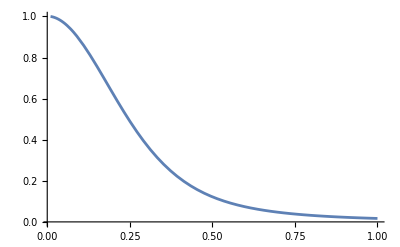

```mathematica
Plot[density[r],{r,0.01,1.0}]
```

### Put TOV solver in function to get M(r)

```mathematica
Clear[M,ρ,EOS,r]
Clear[GetGenericMassRadius,scales]
(* ρcentral  is the central density
EOS is the dimensionful equation of state, function of rho
ρfrac sets the fractional density at which the radius of the NS is defined
scales: first is radius scale, second is density scale, third is mass scale 

dpdr = dpdrho * drhodr  evaluated at rho=rho(r)

Function returns {{\bar{R}, \bar{M}}, {\bar{\rho}(\bar{r}), \bar{M}(\bar{r})}} *)
GetGenericMassRadius[ρcentral_,EOS_,ρfrac_,scales_]:=Module[{dMdr,dPdr,ρc=ρcentral,sols,Rstar,Mstar,mass,density,rstart=0.01*10^4/scales[[1]],rend=5000.0*10^4/scales[[1]],alpha,Acoef,density out,density total,ddensitydr,mass out,mass total,dEOSdrhoofr,EOSscaled,dEOSscaleddrhoofr},
(*EOSscaled[ρ_]:=EOS[ρ*scales[[2]]]/scales[[4]];*)
dEOSdrhoofr[ρ_]:= Evaluate[D[EOS[ρ],ρ]];
dMdr=D[M[r],r]==4*Pi*r^2*ρ[r]*(scales[[1]]^3* scales[[2]]/scales[[3]]);
dPdr=D[ρ[r],r]==-((dEOSdrhoofr[scales[[2]]*ρ[r]])^(-1))*(M[r]+4*Pi*r^3*EOS[ρ[r]*scales[[2]]]*scales[[1]]^3/scales[[3]])*(EOS[ρ[r]*scales[[2]]]/scales[[2]]+ρ[r])/(r*(r*scales[[1]]/scales[[3]]-2*M[r]));
sols=NDSolve[{dMdr,dPdr,M[rstart]==(4/3)*Pi*ρc*rstart^3*scales[[2]]*scales[[1]]^3/scales[[3]],ρ[rstart]==ρc,WhenEvent[ρ[r]==ρc*ρfrac,"StopIntegration"]},{M,ρ},{r,rstart,rend},(*Method->{"StiffnessSwitching",Method->{"ExplicitRungeKutta",Automatic}},AccuracyGoal->5,PrecisionGoal->4*)PrecisionGoal->2][[1]];
mass[r_]:=Evaluate[M[r]/.sols];
density[r_]:=Evaluate[ρ[r]/.sols];
ddensitydr[r_]:=Evaluate[D[density[r],r]];
Rstar=Re[density["Domain"][[1]][[2]]];
Mstar=Re[mass[Rstar]];
alpha=-(ddensitydr[Rstar]/density[Rstar]);
Acoef=density[Rstar];
density out[r_]:=Acoef*Exp[-alpha*(r - Rstar)];
density total[r_]:=If[r<=Rstar,density[r],density out[r]];
mass out[r_]:=Mstar -((Acoef*(-1+Exp[alpha*(-r+Rstar)]))/alpha);
mass total[r_]:=If[r<=Rstar,mass[r],mass out[r]];
{{Rstar,Mstar},{mass total,density total}}]
```

```mathematica
RescaleMRPair km Msun[MRPair_,scales_]:={(MRPair[[1]])*scales[[1]]/10^3, ((MRPair[[2]])*scales[[3]]*clight^2/GN)/Msun}
RescaleMRΛTriplet km Msun dim0[MRΛTriplet_,scales_]:={(MRΛTriplet[[1]])*scales[[1]]/10^3, ((MRΛTriplet[[2]])*scales[[3]]*clight^2/GN)/Msun,MRΛTriplet[[3]]}
RescaleMRPair m Msun[MRPair_,scales_]:={(MRPair[[1]])*scales[[1]], ((MRPair[[2]])*scales[[3]]*clight^2/GN)/Msun}
RescaleMRPair m kg[MRPair_,scales_]:={(MRPair[[1]])*scales[[1]], ((MRPair[[2]]*clight^2/GN)*scales[[1]]^3 * scales[[2]])}
RescaleM kg[mass_,scales_]:=((mass*clight^2/GN)*scales[[1]]^3 * scales[[2]])
RescaleR m[radius_,scales_]:=(radius)*scales[[1]]
```

### Solve for tidal deformability without axion

```mathematica
(* Mfnc is \bar{M}(\bar{r})
ditto for other fncs
scales: first is radius scale, second is density scale, third is mass scale 

dpdr = dpdrho * drhodr  evaluated at rho=rho(r)

Function returns {{\bar{R}, \bar{M}}, {\bar{\rho}(\bar{r}), \bar{M}(\bar{r})}} *)
Clear[GetTidalDeformabilityNoAxions]
GetTidalDeformabilityNoAxions[Mfnc_,ρfnc_,pfnc_,ρprimefnc_,Rstar_,Mstar_,scales_]:=Module[{sols,rstart=0.01*10^4/scales[[1]],yequation,yinit,ysol,yR,Co,tidal deformability},
yequation = (2*(3*r^2*scales[[1]]^2 + 2*(Mfnc[r]^2*scales[[3]]^2 + Pi*r^4*scales[[1]]^4*(pfnc[r]*(-9 + 16*Pi*r^2*scales[[1]]^2*pfnc[r]) - 5*ρfnc[r]*scales[[2]]) + r*scales[[1]]*Mfnc[r]*scales[[3]]*(-3 + 2*Pi*r^2*scales[[1]]^2*(13*pfnc[r] + 5*ρfnc[r]*scales[[2]])) + (Pi*r^4*scales[[1]]^4*(r*scales[[1]] - 2*Mfnc[r]*scales[[3]])^2*ρprimefnc[r]*scales[[2]]/scales[[1]])/(Mfnc[r]*scales[[3]] + 4*Pi*r^3*scales[[1]]^3*pfnc[r]))))/(r*scales[[1]]*(r*scales[[1]] - 2*Mfnc[r]*scales[[3]])) == ((2*y[r]*(r*scales[[1]] - Mfnc[r]*scales[[3]] + 2*Pi*r^3*scales[[1]]^3*(pfnc[r] - ρfnc[r]*scales[[2]])) + r*scales[[1]]*(r*scales[[1]] - 2*Mfnc[r]*scales[[3]])*(y[r]^2/(Rstar*scales[[1]]) + Derivative[1][y][r]/scales[[1]])))/(Rstar*scales[[1]]);
yinit=y[rstart]==2*Rstar/rstart;
sols=NDSolve[{yequation,yinit},{y},{r,rstart,Rstar},PrecisionGoal->2][[1]];
ysol[r_]:=Evaluate[y[r]/.sols];
Print[ysol[r]];
yR = ysol[Rstar];
Co=Mstar*scales[[3]]/(Rstar*scales[[1]]);
tidal deformability=(16*(1 - 2*Co)^2*(2 + 2*Co*(-1 + yR) - yR))/(30*Co*(6 - 3*yR + Co*(3*(-8 + 5*yR) + 2*Co*(13 - 11*yR + Co*(-2 + 3*yR + 2*Co*(1 + yR))))) + 45*(1 - 2*Co)^2*(2 + 2*Co*(-1 + yR) - yR)*Log[1 - 2*Co]);
{{Mstar,tidal deformability}}]
```

### Solve for axion field, energy density, and pressure

```mathematica
(* I need to be careful with units here. I'll go back and be thorough after I have something down. *)
```

```mathematica
rscale=10^19;
fasub=10^16;
masub=10^-20;
```

```mathematica
GetAxionField[massradiussol_,mass_,density_,ma_,fa_,rscale_]:=Module[{density coefficient sub,dθpdr rscaled,dθdr rscaled,mythetaTfncsols,NSradiusscaled,r,rt,θsol,θprimesol},
NSradiusscaled=r/.Normal[Solve[r*(rscale*hbarGeV*clight)/10^3 == massradiussol[[1]]/10^3,{r}][[1]]];
density coefficient sub=((clight^2/GN)*(clight^2/(GeV2joules))*((hbarGeV*clight)^3))*σN/(4*fa^2*mN*ma^2);
dθpdr rscaled = D[θTp[rt],rt]==(ma^2*rscale^2)*(1 - 2*mass[rt*rscale*hbarGeV*clight]/(rt*rscale*hbarGeV*clight))^(-1) * (density[rt*rscale*hbarGeV*clight]*density coefficient sub-1)*Sin[θT[rt]]*(Cos[θT[rt]]/Abs[Cos[θT[rt]]]);
dθdr rscaled = D[θT[rt],rt]==θTp[rt];
mythetaTfncsols=NDSolve[{dθpdr rscaled,dθdr rscaled,θT[NSradiusscaled-10^-14]==1/2,θTp[NSradiusscaled-10^-14]==-ma*rscale/2},{θT, θTp},{rt,0.001,10*NSradiusscaled},PrecisionGoal->20][[1]];
θsol[r_]:=Evaluate[θT/.mythetaTfncsols];
θprimesol[r_]:=Evaluate[θTp/.mythetaTfncsols];
{{θsol,θprimesol}}]
```

```mathematica
GetAxionEnergyAndPressure[θsol_,θprimesol_,massradiussol_,mass_,density_,masub_,fasub_,rscale_]:=Module[{vascaled},
vascaled = -(4*fa^2*ma^2 - σN*density[r]/mN)*Abs[Cos[θsol[r]]];
ρasol[r_]:=Evaluate[(1/2)*(Exp[-νfnc[r]]*θprimesol[r]^2 + 2*vascaled)];
pasol[r_]:=Evaluate[(1/2)*(-Exp[-νfnc[r]]*θprimesol[r]^2 + 2*vascaled)];
{{ρasol,pasol}}]
```

```mathematica
mythetaTfncsols=NDSolve[{dθpdr rscaled,dθdr rscaled,θT[NSradiusscaled-10^-14]==1/2,θTp[NSradiusscaled-10^-14]==-masub*rscale/2},{θT, θTp},{rt,0.001,10*NSradiusscaled},PrecisionGoal->20][[1]];
```

```mathematica
mythetaTfncsols
```

{θT→InterpolatingFunction[…],θTp→InterpolatingFunction[…]}

```mathematica
thetafncin[rt_]:=Evaluate[θT[rt]/.mythetaTfncsols];
thetafncinprime[rt_]:=Evaluate[θTp[rt]/.mythetaTfncsols];
thetafncout[rt_]:=(thetafncin[NSradiusscaled]*NSradiusscaled/Exp[-masub*NSradiusscaled*rscale])*Exp[-masub*rt*rscale]/rt;
thetafncoutprime[rt_]:=Evaluate[D[thetafncout[rt],rt]];

thetafnc[rt_]:=Evaluate[thetafncin[rt]*HeavisideTheta[NSradiusscaled-rt]+thetafncout[rt]*HeavisideTheta[rt-NSradiusscaled]]
thetafncprime[rt_]:=Evaluate[thetafncinprime[rt]*HeavisideTheta[NSradiusscaled-rt]+thetafncoutprime[rt]*HeavisideTheta[rt-NSradiusscaled]]
```

### Solve both M-R and Tidal deformability

```mathematica
GetMRandΛNoAxions[ρcentral_,EOS_,ρfrac_,scales_]:=Module[{dMdr,dPdr,ρc=ρcentral,sols,Rstar,Mstar,mass,density,rstart=0.01*10^4/scales[[1]],rend=5000.0*10^4/scales[[1]],alpha,Acoef,density out,density total,ddensitydr,mass out,mass total,dEOSdrhoofr,EOSscaled,dEOSscaleddrhoofr,yequation,yinit,ysol,pressure,yR,Co,tidal deformability},
(*EOSscaled[ρ_]:=EOS[ρ*scales[[2]]]/scales[[4]];*)
dEOSdrhoofr[ρ_]:= Evaluate[D[EOS[ρ],ρ]];
dMdr=D[M[r],r]==4*Pi*r^2*ρ[r]*(scales[[1]]^3* scales[[2]]/scales[[3]]);
dPdr=D[ρ[r],r]==-((dEOSdrhoofr[scales[[2]]*ρ[r]])^(-1))*(M[r]+4*Pi*r^3*EOS[ρ[r]*scales[[2]]]*scales[[1]]^3/scales[[3]])*(EOS[ρ[r]*scales[[2]]]/scales[[2]]+ρ[r])/(r*(r*scales[[1]]/scales[[3]]-2*M[r]));
sols=NDSolve[{dMdr,dPdr,M[rstart]==(4/3)*Pi*ρc*rstart^3*scales[[2]]*scales[[1]]^3/scales[[3]],ρ[rstart]==ρc,WhenEvent[ρ[r]==ρc*ρfrac,"StopIntegration"]},{M,ρ},{r,rstart,rend},(*Method->{"StiffnessSwitching",Method->{"ExplicitRungeKutta",Automatic}},AccuracyGoal->5,PrecisionGoal->4*)PrecisionGoal->2][[1]];
mass[r_]:=Evaluate[M[r]/.sols];
density[r_]:=Evaluate[ρ[r]/.sols];
ddensitydr[r_]:=Evaluate[D[density[r],r]];
pressure[r_]:=Evaluate[EOS[densityfnc[r]*myscales[[2]]]];
Rstar=Re[density["Domain"][[1]][[2]]];
Mstar=Re[mass[Rstar]];

yequation = (2*(3*r^2*scales[[1]]^2 + 2*(mass[r]^2*scales[[3]]^2 + Pi*r^4*scales[[1]]^4*(pressure[r]*(-9 + 16*Pi*r^2*scales[[1]]^2*pressure[r]) - 5*density[r]*scales[[2]]) + r*scales[[1]]*mass[r]*scales[[3]]*(-3 + 2*Pi*r^2*scales[[1]]^2*(13*pressure[r] + 5*density[r]*scales[[2]])) + (Pi*r^4*scales[[1]]^4*(r*scales[[1]] - 2*mass[r]*scales[[3]])^2*ddensitydr[r]*scales[[2]]/scales[[1]])/(mass[r]*scales[[3]] + 4*Pi*r^3*scales[[1]]^3*pressure[r]))))/(r*scales[[1]]*(r*scales[[1]] - 2*mass[r]*scales[[3]])) == ((2*y[r]*(r*scales[[1]] - mass[r]*scales[[3]] + 2*Pi*r^3*scales[[1]]^3*(pressure[r] - density[r]*scales[[2]])) + r*scales[[1]]*(r*scales[[1]] - 2*mass[r]*scales[[3]])*(y[r]^2/(Rstar*scales[[1]]) + Derivative[1][y][r]/scales[[1]])))/(Rstar*scales[[1]]);
yinit=y[rstart]==2*Rstar/rstart;
sols=NDSolve[{yequation,yinit},{y},{r,rstart,Rstar},PrecisionGoal->2][[1]];
ysol[r_]:=Evaluate[y[r]/.sols];

yR = ysol[Rstar];
Co=Mstar*scales[[3]]/(Rstar*scales[[1]]);
tidal deformability=(16*(1 - 2*Co)^2*(2 + 2*Co*(-1 + yR) - yR))/(30*Co*(6 - 3*yR + Co*(3*(-8 + 5*yR) + 2*Co*(13 - 11*yR + Co*(-2 + 3*yR + 2*Co*(1 + yR))))) + 45*(1 - 2*Co)^2*(2 + 2*Co*(-1 + yR) - yR)*Log[1 - 2*Co]);

alpha=-(ddensitydr[Rstar]/density[Rstar]);
Acoef=density[Rstar];
density out[r_]:=Acoef*Exp[-alpha*(r - Rstar)];
density total[r_]:=If[r<=Rstar,density[r],density out[r]];
mass out[r_]:=Mstar -((Acoef*(-1+Exp[alpha*(-r+Rstar)]))/alpha);
mass total[r_]:=If[r<=Rstar,mass[r],mass out[r]];
{{Rstar,Mstar,tidal deformability},{mass total,density total}}]
```

### Plot A Mass Radius relation

I think that this is working how I want it to work.

IMPORTANT: these equations are the same under the rescaling p → p/ρ_c, ρ → ρ/ρ_c, r → r*sqrt(ρ_c), m → m*sqrt(ρ_c), and k → k*ρ_c^(Γ-1). Note that ρ_c doesn’t need to actually be the central density. It can be whatever we want it to be. What we’ve done here is to assume that everything is dimensionless and find a numerically stable integration region. Then we can just take that region of numerically stable central densities and rescale all the relevant variables by whatever factor is necessary to get physical central densities.

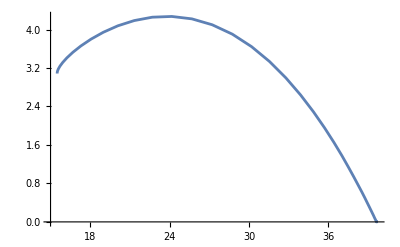

```mathematica
gamma =2.0;
MR vals2 = Table[RescaleMRPair km Msun[GetPolytropeMassRadius[10^ρcentral,1.0,gamma,0.000000001][[1]],10^-9],{ρcentral,-5,1,0.1}];
ListPlot[Re[MR vals2],PlotRange->All(*,ScalingFunctions->{"Log","Log"}*),Joined->True]
```

```mathematica
gamma =5.0/3.0;
MR vals53 = Table[RescaleMRPair km Msun[GetPolytropeMassRadius[10^ρcentral,1.0,gamma,0.0000001][[1]],10^-9],{ρcentral,-3,1,0.1}];
ListPlot[Re[MR vals53],PlotRange->All(*,ScalingFunctions->{"Log","Log"}*),Joined->False]
```

$Aborted

ListPlot[Re(MR vals53),PlotRange→All,Joined→False]

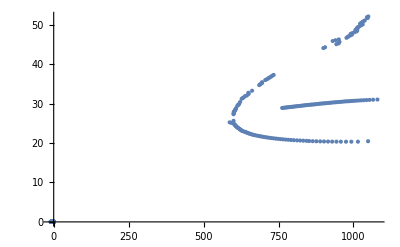

```mathematica
gamma =4.0/3.0;
MR vals43 = Table[RescaleMRPair km Msun[GetPolytropeMassRadius[10^ρcentral,1.0,gamma,0.0000001][[1]],10^-9],{ρcentral,-3,1,0.01}];
ListPlot[Re[MR vals43],PlotRange->All(*,ScalingFunctions->{"Log","Log"}*),Joined->False]
```

### Solve for Mr relation with generic function

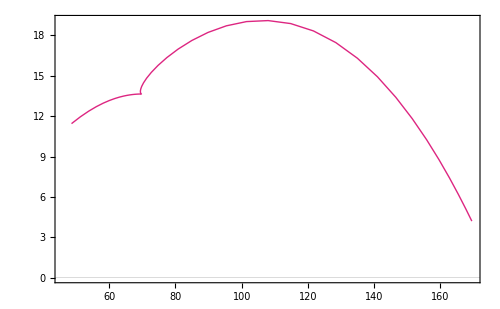

```mathematica
gamma =2.0;
kappa = 2.0*10^10;
myEOS[ρ_]:=kappa*ρ^gamma;
myscales={10^3,10^-10,10^3};

MR vals2 = Table[RescaleMRPair km Msun[GetGenericMassRadius[10^ρcentral,myEOS,10^-5,myscales][[1]],myscales],{ρcentral,-2,4,0.1}];
ListPlot[Re[MR vals2],PlotRange->All,Joined->True,PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}R \\ \\left[\\text{km} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}M \\ \\left[M_{\\odot} \\right]",Magnification->2.3]},PlotStyle->{{c3,Thick},{c3,Thick},{c5,Thick},{c2,Dashed,Thick}},ImageSize->{500,400}]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/M-R-polytrope-2.pdf",%,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/M-R-polytrope-2.pdf

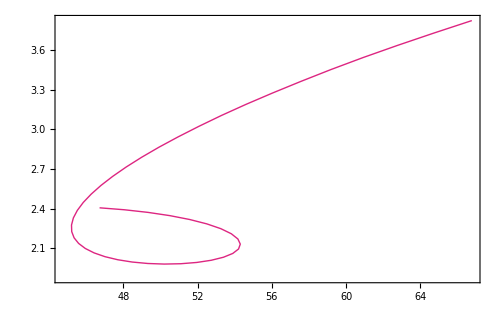

```mathematica
gamma =4.0/3.0;
kappa =0.1*(10^(10/3));
myEOS[ρ_]:=kappa*ρ^gamma;
myscales={10^2,10^-10,10^2};

MR vals2 = Table[RescaleMRPair km Msun[GetGenericMassRadius[10^ρcentral,myEOS,10^-5,myscales][[1]],myscales],{ρcentral,0.7,3.0,0.05}];
ListPlot[Re[MR vals2],PlotRange->All,Joined->True,PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}R \\ \\left[\\text{km} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}M \\ \\left[M_{\\odot} \\right]",Magnification->2.3]},PlotStyle->{{c3,Thick},{c3,Thick},{c5,Thick},{c2,Dashed,Thick}},ImageSize->{500,400}]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/M-R-polytrope-4on3.pdf",%,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/M-R-polytrope-4on3.pdf

### Check TOV solver with known EOS

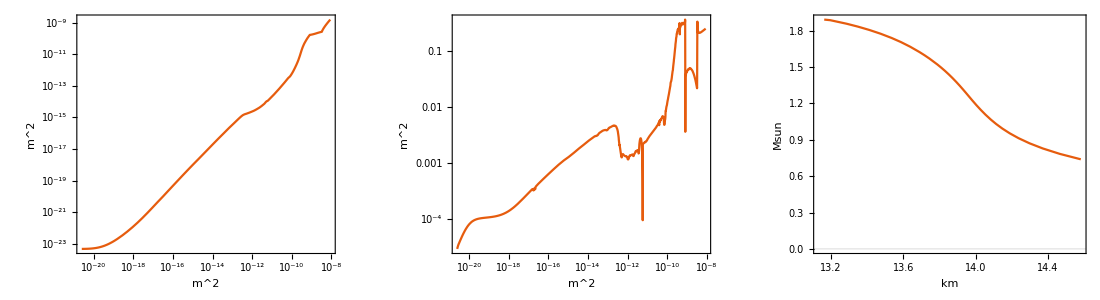

```mathematica
(* start by importing the EOS data *)
FILEBASE="eos_nb0.065_G0.01_nb_0.23_G_0.06";
EOSPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/output_stable_eos_files_p_of_nb_fixed/";
EOSData=Import[StringJoin[EOSPATH,FILEBASE,".csv"],"CSV"];
MRData=Import[StringJoin[MRPATH,FILEBASE,"_observables.dat"](*,"CSV"*)];
EOSDataLimited=EOSData[[1;;Dimensions[EOSData][[1]],8;;9]];
MRDataLimited=MRData[[1;;Dimensions[MRData][[1]],2;;3]];
pressureEOS=Interpolation[EOSDataLimited]; (* rho and p are in MeV / fm^3, so we need to rescale *) 
(* I actually shouldn't need to rescale. That should just be wrapped up in whatever I choose as my ρscale variable in the TOV solver. *)
dpressureEOS[ρ_]:=Evaluate[D[pressureEOS[ρ],ρ]];
maxdensity=Max[EOSDataLimited[[1;;Dimensions[EOSData][[1]],1]]];
mindensity=Min[EOSDataLimited[[1;;Dimensions[EOSData][[1]],1]]];
pressureEOS m2[rhobar_]:=pressureEOS[rhobar/(MeVperfm3 2 Jperm3*Jperm3 2 m2)]*(MeVperfm3 2 Jperm3*Jperm3 2 m2)
dpressureEOS m2[ρ_]:=Evaluate[D[pressureEOS m2[ρ],ρ]];
domainscaled={mindensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2),maxdensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2)};
MRfnc=Interpolation[MRDataLimited];

EOSplot = LogLogPlot[pressureEOS m2[ρ],{ρ,domainscaled[[1]],domainscaled[[2]]},PlotTheme->"Scientific",FrameLabel->{"m^2","m^2"}];
EOSderivativePlot = LogLogPlot[dpressureEOS m2[ρ],{ρ,domainscaled[[1]],domainscaled[[2]]},PlotTheme->"Scientific",FrameLabel->{"m^2","m^2"},PerformanceGoal->"Quality"];
MRplot = ListPlot[MRDataLimited,PlotTheme->"Scientific",Joined->True,FrameLabel->{"km","Msun"}];
GraphicsRow[{EOSplot,EOSderivativePlot,MRplot},ImageSize->{1100,300}]
```

```mathematica
myscales={10^5,10^-10,10^1};
MR vals2 = Table[RescaleMRPair km Msun[GetGenericMassRadius[ρc,pressureEOS m2,10^-10,myscales][[1]],myscales],{ρc,3.0,8.5,0.1}];
```

InterpolatingFunction::dmval: Input value {-71.6486} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.28849×10^15} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

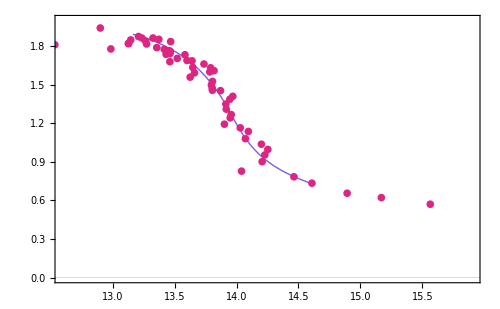

```mathematica
ListPlot[{Re[MR vals2],MRDataLimited},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}R \\ \\left[\\text{km} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}M \\ \\left[M_{\\odot} \\right]",Magnification->2.3]},PlotStyle->{{c3,Thick},{c2,Thick},{c5,Thick},{c2,Dashed,Thick}},Joined->{False,True},ImageSize->{500,400},PlotRange->{{12.6,15.9},{0.0,2.0}}(*All*)]
```

### Check TOV solver with known EOS --- second EOS

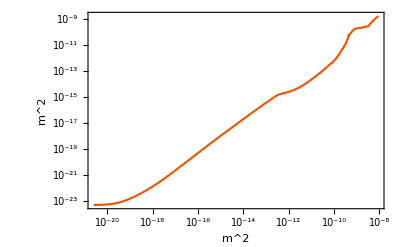

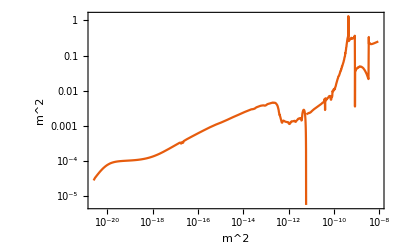

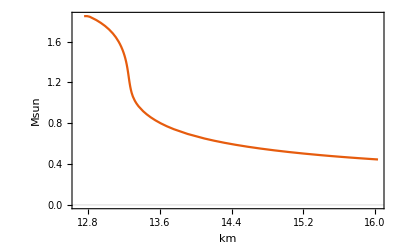

```mathematica
(* start by importing the EOS data *)
FILEBASE="eos_nb0.085_G0.01_nb_0.31_G_0.05";
EOSPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/output_stable_eos_files_p_of_nb_fixed/";
EOSData=Import[StringJoin[EOSPATH,FILEBASE,".csv"],"CSV"];
MRData=Import[StringJoin[MRPATH,FILEBASE,"_observables.dat"](*,"CSV"*)];
EOSDataLimited=EOSData[[1;;Dimensions[EOSData][[1]],8;;9]];
MRDataLimited=MRData[[1;;Dimensions[MRData][[1]],2;;3]];
pressureEOS=Interpolation[EOSDataLimited]; (* rho and p are in MeV / fm^3, so we need to rescale *) 
(* I actually shouldn't need to rescale. That should just be wrapped up in whatever I choose as my ρscale variable in the TOV solver. *)
dpressureEOS[ρ_]:=Evaluate[D[pressureEOS[ρ],ρ]];
maxdensity=Max[EOSDataLimited[[1;;Dimensions[EOSData][[1]],1]]];
mindensity=Min[EOSDataLimited[[1;;Dimensions[EOSData][[1]],1]]];
pressureEOS m2[rhobar_]:=pressureEOS[rhobar/(MeVperfm3 2 Jperm3*Jperm3 2 m2)]*(MeVperfm3 2 Jperm3*Jperm3 2 m2)
dpressureEOS m2[ρ_]:=Evaluate[D[pressureEOS m2[ρ],ρ]];
domainscaled={mindensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2),maxdensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2)};
MRfnc=Interpolation[MRDataLimited];

LogLogPlot[pressureEOS m2[ρ],{ρ,domainscaled[[1]],domainscaled[[2]]},PlotTheme->"Scientific",FrameLabel->{"m^2","m^2"}]
LogLogPlot[dpressureEOS m2[ρ],{ρ,domainscaled[[1]],domainscaled[[2]]},PlotTheme->"Scientific",FrameLabel->{"m^2","m^2"},PerformanceGoal->"Quality"]
ListPlot[MRDataLimited,PlotTheme->"Scientific",Joined->True,FrameLabel->{"km","Msun"}]
```

```mathematica
myscales={10^5,10^-10,10};
MR vals2 = Table[RescaleMRPair km Msun[GetGenericMassRadius[ρc,pressureEOS m2,10^-10,myscales][[1]],myscales],{ρc,3.0,8.5,0.1}];
```

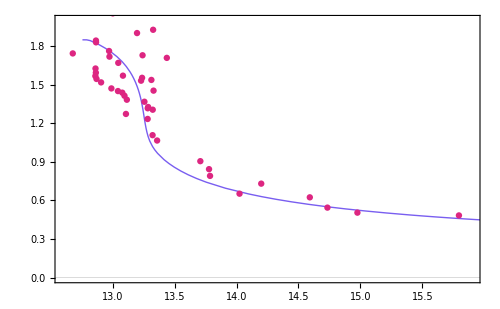

```mathematica
ListPlot[{Re[MR vals2],MRDataLimited},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}R \\ \\left[\\text{km} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}M \\ \\left[M_{\\odot} \\right]",Magnification->2.3]},PlotStyle->{{c3,Thick},{c2,Thick},{c5,Thick},{c2,Dashed,Thick}},Joined->{False,True},ImageSize->{500,400},PlotRange->{{12.6,15.9},{0.0,2.0}}(*All*)]
```

# Tidal Deformability Solver

#### Load EOS

```mathematica
FILEBASE="eos_nb0.085_G0.01_nb_0.31_G_0.05";
EOSPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/output_stable_eos_files_p_of_nb_fixed/";
EOSData=Import[StringJoin[EOSPATH,FILEBASE,".csv"],"CSV"];
MRData=Import[StringJoin[MRPATH,FILEBASE,"_observables.dat"](*,"CSV"*)];
EOSDataLimited=EOSData[[1;;Dimensions[EOSData][[1]],8;;9]];
MRDataLimited=MRData[[1;;Dimensions[MRData][[1]],2;;3]];
pressureEOS=Interpolation[EOSDataLimited]; (* rho and p are in MeV / fm^3, so we need to rescale *) 
(* I actually shouldn't need to rescale. That should just be wrapped up in whatever I choose as my ρscale variable in the TOV solver. *)
dpressureEOS[ρ_]:=Evaluate[D[pressureEOS[ρ],ρ]];
maxdensity=Max[EOSDataLimited[[1;;Dimensions[EOSData][[1]],1]]];
mindensity=Min[EOSDataLimited[[1;;Dimensions[EOSData][[1]],1]]];
pressureEOS m2[rhobar_]:=pressureEOS[rhobar/(MeVperfm3 2 Jperm3*Jperm3 2 m2)]*(MeVperfm3 2 Jperm3*Jperm3 2 m2)
dpressureEOS m2[ρ_]:=Evaluate[D[pressureEOS m2[ρ],ρ]];
domainscaled={mindensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2),maxdensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2)};
MRfnc=Interpolation[MRDataLimited];
```

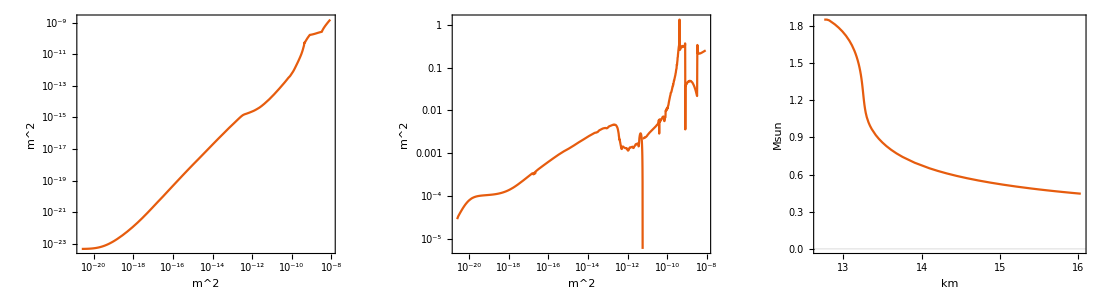

```mathematica
EOSplot = LogLogPlot[pressureEOS m2[ρ],{ρ,domainscaled[[1]],domainscaled[[2]]},PlotTheme->"Scientific",FrameLabel->{"m^2","m^2"}];
EOSderivativePlot = LogLogPlot[dpressureEOS m2[ρ],{ρ,domainscaled[[1]],domainscaled[[2]]},PlotTheme->"Scientific",FrameLabel->{"m^2","m^2"},PerformanceGoal->"Quality"];
MRplot = ListPlot[MRDataLimited,PlotTheme->"Scientific",Joined->True,FrameLabel->{"km","Msun"}];
GraphicsRow[{EOSplot,EOSderivativePlot,MRplot},ImageSize->{1100,300}]
```

#### Solve for Mass & radius

```mathematica
(* outputs: {{radius, mass}, {mass, density}} *)
(* units are geometrized rescaled by density in the last argument *)
myscales={10^5,10^-10,10};
sols=GetGenericMassRadius[5.0,pressureEOS m2,10^-8,myscales];
```

InterpolatingFunction::dmval: Input value {-21.2818} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.91485×10^13} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
massradius=RescaleMRPair m Msun[sols[[1]],myscales](*sols[[1]]*)
```

{13232.1,1.36851}

```mathematica
massradius unscaled = sols[[1]]
```

{0.132321,202.008}

#### Define scaled functions

```mathematica
massfnc[r_]:=Evaluate[sols[[2]][[1]][r]]
densityfnc[r_]:=Evaluate[sols[[2]][[2]][r]]
pressurefnc[r_]:=Evaluate[pressureEOS m2[densityfnc[r]*myscales[[2]]]]
densityfnc derivative[r_]:=Evaluate[D[densityfnc scaled[r],r]]
```

```mathematica
massradius unscaled
```

{0.132321,202.008}

#### Solve for λ

```mathematica
GetTidalDeformabilityNoAxions[massfnc,densityfnc,pressurefnc,densityfnc derivative,massradius unscaled[[1]],massradius unscaled[[2]],myscales]
```

InterpolatingFunction[…][r]

{{202.008,563.195}}

#### Solver for R-M-Λ with total function

```mathematica
myscales={10^5,10^-10,10};
GetMRandΛNoAxions[5.0,pressureEOS m2,10^-8,myscales]
```

InterpolatingFunction::dmval: Input value {-128.349} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.57351×10^16} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.138134,214.747,540.956},{mass total$150574,density total$150574}}

### Check Λ solver with known EOS #1

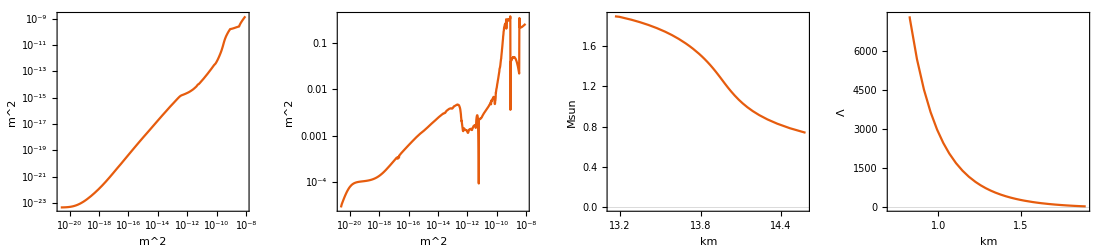

```mathematica
(* start by importing the EOS data *)
FILEBASE="eos_nb0.065_G0.01_nb_0.23_G_0.06";
EOSPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/output_stable_eos_files_p_of_nb_fixed/";
EOSData=Import[StringJoin[EOSPATH,FILEBASE,".csv"],"CSV"];
MRData=Import[StringJoin[MRPATH,FILEBASE,"_observables.dat"](*,"CSV"*)];
EOSDataLimited=EOSData[[1;;Dimensions[EOSData][[1]],8;;9]];
MRDataLimited=MRData[[1;;Dimensions[MRData][[1]],{2,3}]];
MΛDataLimited=MRData[[1;;Dimensions[MRData][[1]],{3,5}]];
pressureEOS=Interpolation[EOSDataLimited]; (* rho and p are in MeV / fm^3, so we need to rescale *) 
(* I actually shouldn't need to rescale. That should just be wrapped up in whatever I choose as my ρscale variable in the TOV solver. *)
dpressureEOS[ρ_]:=Evaluate[D[pressureEOS[ρ],ρ]];
maxdensity=Max[EOSDataLimited[[1;;Dimensions[EOSData][[1]],1]]];
mindensity=Min[EOSDataLimited[[1;;Dimensions[EOSData][[1]],1]]];
pressureEOS m2[rhobar_]:=pressureEOS[rhobar/(MeVperfm3 2 Jperm3*Jperm3 2 m2)]*(MeVperfm3 2 Jperm3*Jperm3 2 m2)
dpressureEOS m2[ρ_]:=Evaluate[D[pressureEOS m2[ρ],ρ]];
domainscaled={mindensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2),maxdensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2)};
MRfnc=Interpolation[MRDataLimited];

EOSplot = LogLogPlot[pressureEOS m2[ρ],{ρ,domainscaled[[1]],domainscaled[[2]]},PlotTheme->"Scientific",FrameLabel->{"m^2","m^2"}];
EOSderivativePlot = LogLogPlot[dpressureEOS m2[ρ],{ρ,domainscaled[[1]],domainscaled[[2]]},PlotTheme->"Scientific",FrameLabel->{"m^2","m^2"},PerformanceGoal->"Quality"];
MRplot = ListPlot[MRDataLimited,PlotTheme->"Scientific",Joined->True,FrameLabel->{"km","Msun"}];
MΛplot = ListPlot[MΛDataLimited,PlotTheme->"Scientific",Joined->True,FrameLabel->{"km","Λ"}];
GraphicsRow[{EOSplot,EOSderivativePlot,MRplot,MΛplot},ImageSize->{1100,250}]
```

```mathematica
myscales={10^5,10^-10,10^1};
MRΛ vals2 = Table[RescaleMRΛTriplet km Msun dim0[Quiet[GetMRandΛNoAxions[ρc,pressureEOS m2,10^-10,myscales][[1]]],myscales],{ρc,3.0,8.5,0.1}];
```

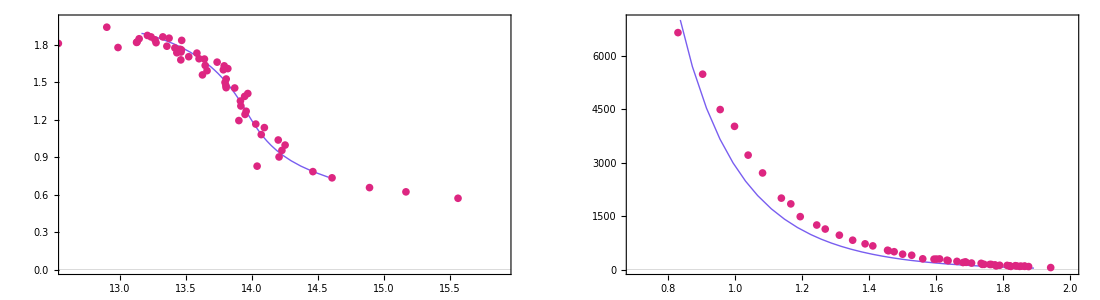

```mathematica
MRplot = ListPlot[{Re[MRΛ vals2[[All,1;;2]]],MRDataLimited},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}R \\ \\left[\\text{km} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}M \\ \\left[M_{\\odot} \\right]",Magnification->2.3]},PlotStyle->{{c3,Thick},{c2,Thick},{c5,Thick},{c2,Dashed,Thick}},Joined->{False,True},ImageSize->{500,400},PlotRange->{{12.6,15.9},{0.0,2.0}}(*All*)];
MΛplot = ListPlot[{Re[MRΛ vals2[[All,2;;3]]],MΛDataLimited},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}M \\ \\left[M_{\\odot} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}\\Lambda",Magnification->2.3]},PlotStyle->{{c3,Thick},{c2,Thick},{c5,Thick},{c2,Dashed,Thick}},Joined->{False,True},ImageSize->{500,400},PlotRange->{{0.7,2.0},{0.0,7000.0}}(*All*)];
GraphicsRow[{MRplot,MΛplot},ImageSize->{1100,300}]
```

### Check Λ solver with known EOS #2

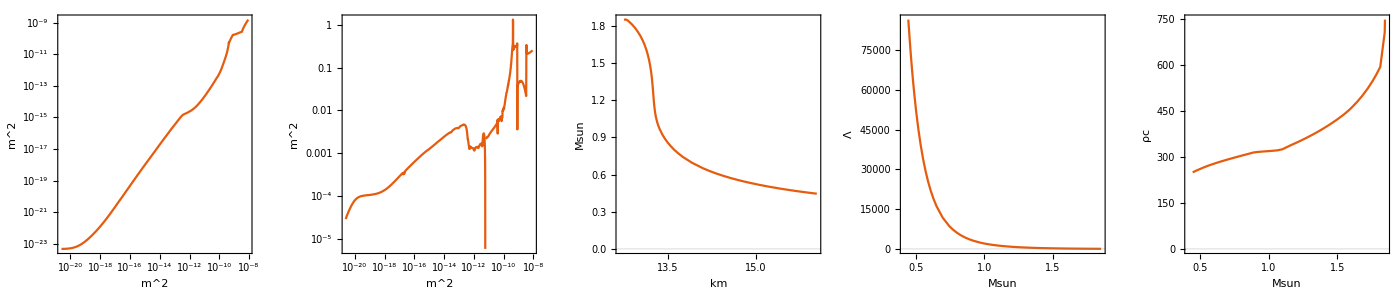

```mathematica
(* start by importing the EOS data *)
FILEBASE="eos_nb0.085_G0.01_nb_0.31_G_0.05";
EOSPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/output_stable_eos_files_p_of_nb_fixed/";
EOSData=Import[StringJoin[EOSPATH,FILEBASE,".csv"],"CSV"];
MRData=Import[StringJoin[MRPATH,FILEBASE,"_observables.dat"](*,"CSV"*)];
EOSDataLimited=EOSData[[1;;Dimensions[EOSData][[1]],8;;9]];
MRDataLimited=MRData[[1;;Dimensions[MRData][[1]],{2,3}]];
MΛDataLimited=MRData[[1;;Dimensions[MRData][[1]],{3,5}]];
MρDataLimited=MRData[[1;;Dimensions[MRData][[1]],{3,1}]];
pressureEOS=Interpolation[EOSDataLimited]; (* rho and p are in MeV / fm^3, so we need to rescale *) 
(* I actually shouldn't need to rescale. That should just be wrapped up in whatever I choose as my ρscale variable in the TOV solver. *)
dpressureEOS[ρ_]:=Evaluate[D[pressureEOS[ρ],ρ]];
maxdensity=Max[EOSDataLimited[[1;;Dimensions[EOSData][[1]],1]]];
mindensity=Min[EOSDataLimited[[1;;Dimensions[EOSData][[1]],1]]];
pressureEOS m2[rhobar_]:=pressureEOS[rhobar/(MeVperfm3 2 Jperm3*Jperm3 2 m2)]*(MeVperfm3 2 Jperm3*Jperm3 2 m2)
dpressureEOS m2[ρ_]:=Evaluate[D[pressureEOS m2[ρ],ρ]];
domainscaled={mindensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2),maxdensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2)};
MRfnc=Interpolation[MRDataLimited];

EOSplot = LogLogPlot[pressureEOS m2[ρ],{ρ,domainscaled[[1]],domainscaled[[2]]},PlotTheme->"Scientific",FrameLabel->{"m^2","m^2"}];
EOSderivativePlot = LogLogPlot[dpressureEOS m2[ρ],{ρ,domainscaled[[1]],domainscaled[[2]]},PlotTheme->"Scientific",FrameLabel->{"m^2","m^2"},PerformanceGoal->"Quality"];
MRplot = ListPlot[MRDataLimited,PlotTheme->"Scientific",Joined->True,FrameLabel->{"km","Msun"}];
MΛplot = ListPlot[MΛDataLimited,PlotTheme->"Scientific",Joined->True,FrameLabel->{"Msun","Λ"}];
Mρplot = ListPlot[MρDataLimited,PlotTheme->"Scientific",Joined->True,FrameLabel->{"Msun","ρc"}];
GraphicsRow[{EOSplot,EOSderivativePlot,MRplot,MΛplot,Mρplot},ImageSize->{1400,300}]
```

```mathematica
myscales={10^5,10^-10,10^1};
MRΛ vals2 = Table[RescaleMRΛTriplet km Msun dim0[Quiet[GetMRandΛNoAxions[ρc,pressureEOS m2,10^-10,myscales][[1]]],myscales],{ρc,3.0,8.5,0.1}];
```

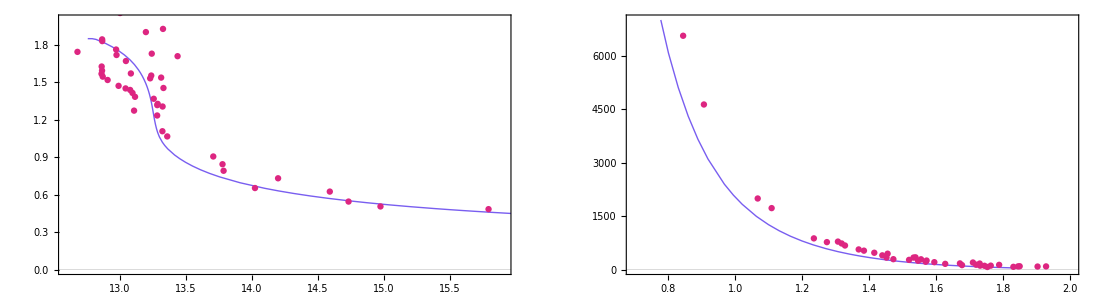

```mathematica
MRplot = ListPlot[{Re[MRΛ vals2[[All,1;;2]]],MRDataLimited},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}R \\ \\left[\\text{km} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}M \\ \\left[M_{\\odot} \\right]",Magnification->2.3]},PlotStyle->{{c3,Thick},{c2,Thick},{c5,Thick},{c2,Dashed,Thick}},Joined->{False,True},ImageSize->{500,400},PlotRange->{{12.6,15.9},{0.0,2.0}}(*All*)];
MΛplot = ListPlot[{Re[MRΛ vals2[[All,2;;3]]],MΛDataLimited},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}M \\ \\left[M_{\\odot} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}\\Lambda",Magnification->2.3]},PlotStyle->{{c3,Thick},{c2,Thick},{c5,Thick},{c2,Dashed,Thick}},Joined->{False,True},ImageSize->{500,400},PlotRange->{{0.7,2.0},{0.0,7000.0}}(*All*)];
GraphicsRow[{MRplot,MΛplot},ImageSize->{1100,300}]
```

# axion solver

This section is meant to take the density and mass functions from the TOV solver and use them to solve for the axion field on the NS background.

IMPORTANT: the TOV equations are solved in geometrized units, but we’ll solve for the axion field in natural units. We’ll also normalize the units by nucleon-related quantities.

### Solve for mass and density

#### EOS stuff

```mathematica
FILEBASE="eos_nb0.085_G0.01_nb_0.31_G_0.05";
EOSPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/output_stable_eos_files_p_of_nb_fixed/";
EOSData=Import[StringJoin[EOSPATH,FILEBASE,".csv"],"CSV"];
MRData=Import[StringJoin[MRPATH,FILEBASE,"_observables.dat"](*,"CSV"*)];
EOSDataLimited=EOSData[[1;;Dimensions[EOSData][[1]],8;;9]];
MRDataLimited=MRData[[1;;Dimensions[MRData][[1]],2;;3]];
pressureEOS=Interpolation[EOSDataLimited]; (* rho and p are in MeV / fm^3, so we need to rescale *) 
(* I actually shouldn't need to rescale. That should just be wrapped up in whatever I choose as my ρscale variable in the TOV solver. *)
dpressureEOS[ρ_]:=Evaluate[D[pressureEOS[ρ],ρ]];
maxdensity=Max[EOSDataLimited[[1;;Dimensions[EOSData][[1]],1]]];
mindensity=Min[EOSDataLimited[[1;;Dimensions[EOSData][[1]],1]]];
pressureEOS m2[rhobar_]:=pressureEOS[rhobar/(MeVperfm3 2 Jperm3*Jperm3 2 m2)]*(MeVperfm3 2 Jperm3*Jperm3 2 m2)
dpressureEOS m2[ρ_]:=Evaluate[D[pressureEOS m2[ρ],ρ]];
domainscaled={mindensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2),maxdensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2)};
MRfnc=Interpolation[MRDataLimited];
```

```mathematica
EOSplot = LogLogPlot[pressureEOS m2[ρ],{ρ,domainscaled[[1]],domainscaled[[2]]},PlotTheme->"Scientific",FrameLabel->{"m^2","m^2"}];
EOSderivativePlot = LogLogPlot[dpressureEOS m2[ρ],{ρ,domainscaled[[1]],domainscaled[[2]]},PlotTheme->"Scientific",FrameLabel->{"m^2","m^2"},PerformanceGoal->"Quality"];
MRplot = ListPlot[MRDataLimited,PlotTheme->"Scientific",Joined->True,FrameLabel->{"km","Msun"}];
GraphicsRow[{EOSplot,EOSderivativePlot,MRplot},ImageSize->{1100,300}]
```

-Graphics-

```mathematica
(* outputs: {{radius, mass}, {mass, density}} *)
(* units are geometrized rescaled by density in the last argument *)
myscales={10^5,10^-10,10};
sols=GetGenericMassRadius[5.0,pressureEOS m2,10^-8,myscales];
```

InterpolatingFunction::dmval: Input value {-21.2818} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.91485×10^13} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
massradius=RescaleMRPair m Msun[sols[[1]],myscales](*sols[[1]]*)
```

{13232.1,1.36851}

```mathematica
massfnc scaled[r_]:=Evaluate[sols[[2]][[1]][r/myscales[[1]]]*myscales[[3]]]
densityfnc scaled[r_]:=Evaluate[sols[[2]][[2]][r/myscales[[1]]]*myscales[[2]]]
densityfnc derivative scaled[r_]:=Evaluate[D[densityfnc scaled[r],r]]

nufnc[r_]:=If[r>=massradius[[1]],Log[(1 - 2*massfnc scaled[massradius[[1]]]/r)],Log[(1 - 2*massfnc scaled[massradius[[1]]]/massradius[[1]])]+NIntegrate[(2*massfnc scaled[rp]+8*Pi*rp^3*pressureEOS m2[densityfnc scaled[rp]])/(rp*(rp-2*massfnc scaled[rp])),{rp,massradius[[1]],r},Method->"GlobalAdaptive",MaxPoints->10^5,PrecisionGoal->2]]

grr[r_]:=Evaluate[-1/(1 - 2*massfnc scaled[r]/r)]
gtt[r_]:=Evaluate[Exp[nufnc[r]]]

grrschw[r_]:=Evaluate[-1/(1 - 2*massfnc scaled[massradius[[1]]]/r)]
gttschw[r_]:=(1 - 2*massfnc scaled[massradius[[1]]]/r)
```

```mathematica
densitynormvals=Table[{r/massradius[[1]],densityfnc scaled[r] / densityfnc scaled[0.01*massradius[[1]]]},{r,0.01*massradius[[1]],1.2*massradius[[1]],massradius[[1]]/1000}];
densityvals=Table[{r/massradius[[1]],densityfnc scaled[r]},{r,0.01*massradius[[1]],1.2*massradius[[1]],massradius[[1]]/1000}];
densityderivativenormvals=Table[{r/massradius[[1]],densityfnc derivative scaled[r]},{r,0.01*massradius[[1]],1.2*massradius[[1]],massradius[[1]]/1000}];
pressurenormvals=Table[{r/massradius[[1]],pressureEOS m2[densityfnc scaled[r]] /pressureEOS m2[densityfnc scaled[0.01*massradius[[1]]]]},{r,0.01*massradius[[1]],1.2*massradius[[1]],massradius[[1]]/1000}];
pressurevals=Table[{r/massradius[[1]],pressureEOS m2[densityfnc scaled[r]]},{r,0.01*massradius[[1]],1.2*massradius[[1]],massradius[[1]]/1000}];
massnormvals=Table[{r/massradius[[1]],massfnc scaled[r]/massfnc scaled[massradius[[1]]]},{r,0.01*massradius[[1]],1.2*massradius[[1]],massradius[[1]]/1000}];
massvals=Table[{r/massradius[[1]],massfnc scaled[r]},{r,0.01*massradius[[1]],1.2*massradius[[1]],massradius[[1]]/1000}];
```

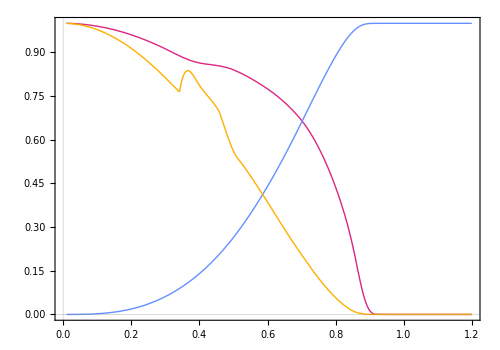

```mathematica
massdensityplot= ListPlot[{densitynormvals,massnormvals,pressurenormvals},PlotRange->All,Joined->True,PlotTheme->"Scientific",FrameTicks->(*{{yticks,yticksNV},{xticks,xticksNV}}*)Automatic,FrameLabel->{MaTeX["\\color{darkgray}r/r_{\\rm NS} \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}\\left[\\text{a.u.} \\right]",Magnification->2.0]},PlotStyle->{{c3,Thick},{c1,Thick},{c5,Thick},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}\\rho(r)",Magnification->1.5],MaTeX["\\color{darkgray}m(r)",Magnification->1.5],MaTeX["\\color{darkgray}p(r)",Magnification->1.5]}]
(*metricplot= ListPlot[{metricvals},PlotRange->All,Joined->True,PlotTheme->"Scientific",FrameTicks->(*{{yticks,yticksNV},{xticks,xticksNV}}*)Automatic,FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}g_{rr} \\ \\left[\\text{a.u.} \\right]",Magnification->2.0]},PlotStyle->{{c3,Thick},{c1,Thick},{c5,Dashed},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full]*)
```

```mathematica
(* why is density dropping to zero and then jumping back up? *)
```

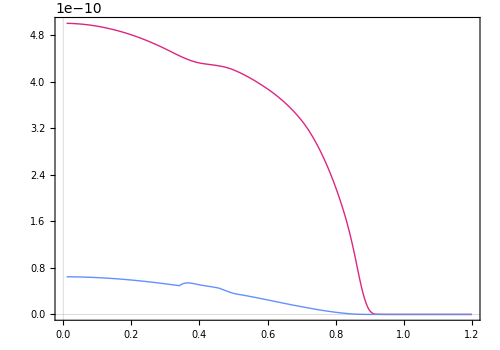

```mathematica
densityderivativeplot= ListPlot[{densityvals,pressurevals},PlotRange->All,Joined->True,PlotTheme->"Scientific",FrameTicks->(*{{yticks,yticksNV},{xticks,xticksNV}}*)Automatic,FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}\\left[\\text{a.u.} \\right]",Magnification->2.0]},PlotStyle->{{c3,Thick},{c1,Thick},{c5,Thick},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}\\rho(r)",Magnification->1.5],MaTeX["\\color{darkgray}p(r)",Magnification->1.5]}]
```

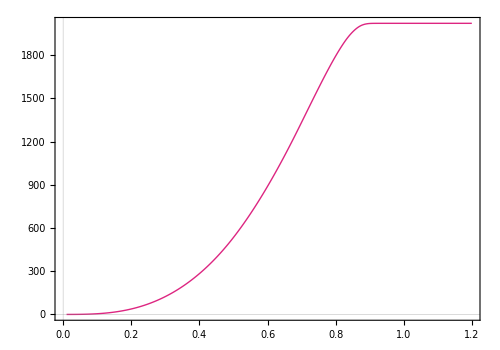

```mathematica
densityderivativeplot= ListPlot[{massvals},PlotRange->All,Joined->True,PlotTheme->"Scientific",FrameTicks->(*{{yticks,yticksNV},{xticks,xticksNV}}*)Automatic,FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}\\left[\\text{a.u.} \\right]",Magnification->2.0]},PlotStyle->{{c3,Thick},{c1,Thick},{c5,Thick},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}\\rho(r)",Magnification->1.5],MaTeX["\\color{darkgray}m(r)",Magnification->1.5],MaTeX["\\color{darkgray}p(r)",Magnification->1.5]}]
```

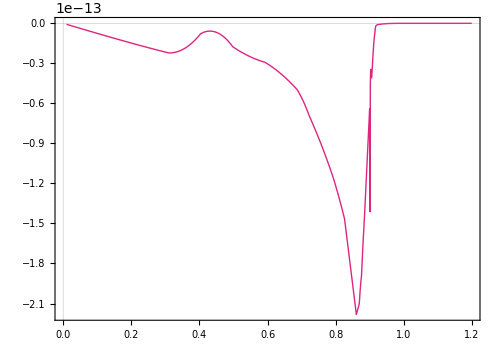

```mathematica
densityderivativeplot= ListPlot[{densityderivativenormvals},PlotRange->All,Joined->True,PlotTheme->"Scientific",FrameTicks->(*{{yticks,yticksNV},{xticks,xticksNV}}*)Automatic,FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}\\left[\\text{a.u.} \\right]",Magnification->2.0]},PlotStyle->{{c3,Thick},{c1,Thick},{c5,Thick},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}\\rho(r)",Magnification->1.5],MaTeX["\\color{darkgray}m(r)",Magnification->1.5],MaTeX["\\color{darkgray}p(r)",Magnification->1.5]}]
```

#### metric stuff

```mathematica
(* it looks a lot like there is a kink in the density and possibly the mass which I really don't want. *)
(* yeah definitely a discontinuity. Also the derivative values are enormous, so something is wrong there. *)
```

```mathematica
gttvals=Table[{r,gtt[r]},{r,0.01*massradius[[1]],2*massradius[[1]],massradius[[1]]/500}];
grrvals=Table[{r,grr[r]},{r,0.01*massradius[[1]],2*massradius[[1]],massradius[[1]]/1000}];
gttschwvals=Table[{r,gttschw[r]},{r,0.5*massradius[[1]],2*massradius[[1]],massradius[[1]]/1000}];
grrschwvals=Table[{r,grrschw[r]},{r,0.5*massradius[[1]],2*massradius[[1]],massradius[[1]]/1000}];
```

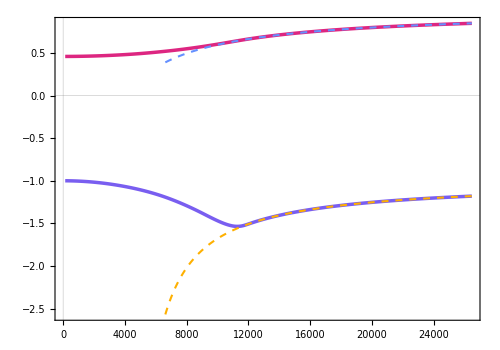

```mathematica
metricelementsplot= ListPlot[{gttvals,grrvals,gttschwvals,grrschwvals},PlotRange->All,Joined->True,PlotTheme->"Scientific",FrameTicks->Automatic,FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}\\left[\\text{a.u.} \\right]",Magnification->2.0]},PlotStyle->{{c3,Thickness[0.005]},{c2,Thickness[0.005]},{c1,Dashed,Thickness[0.003]},{c5,Dashed,Thickness[0.003]}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}g_{tt}",Magnification->1.5],MaTeX["\\color{darkgray}g_{rr}",Magnification->1.5],MaTeX["\\color{darkgray}g_{tt} \\ schw",Magnification->1.5],MaTeX["\\color{darkgray}g_{rr} \\ schw",Magnification->1.5]}]
```

```mathematica
(* this is for sure wrong and not what I was getting before. Why is everything broken??????????? *)
(* *)
```

```mathematica
(* why doesn't the tt comnponent agree nicely? *)
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/normalized-mass-and-density.pdf",massdensityplot,"PDF"]
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/tov-vs-schwarzschild-metric.pdf",metricelementsplot,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/normalized-mass-and-density.pdf

/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/tov-vs-schwarzschild-metric.pdf

### What does the zero density solution look like

```mathematica
(* might need to rescale radius by the mass to get numerical stability *)
```

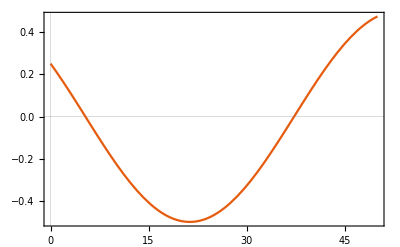

```mathematica
rscale=10^19;
fasub=10^16;
masub=10^-20;
density coefficient sub=((clight^2/GN)*(clight^2/(GeV2joules))*((hbarGeV*clight)^3))*σN/(4*fasub^2*mN*masub^2);
dθpdr rscaled = D[θTp[rt],rt]==(masub^2*rscale^2)*(1 (*- 2*massfnc scaled[rt*rscale*hbarGeV*clight]/(rt*rscale*hbarGeV*clight)*))^(-1) * ((*densityfnc scaled[rt*rscale*hbarGeV*clight]*density coefficient sub*)-1)*Sin[θT[rt]]*(Cos[θT[rt]]/Abs[Cos[θT[rt]]]);
dθdr rscaled = D[θT[rt],rt]==θTp[rt];

mythetaTfncsols=NDSolve[{dθpdr rscaled,dθdr rscaled,θT[500]==0.5,θTp[500]==0.0},{θT, θTp},{rt,0.001,500},PrecisionGoal->20][[1]];
thetafnc[rt_]:=Evaluate[θT[rt]/.mythetaTfncsols]

Plot[thetafnc[r],{r,0.001,50},PlotRange->All,PlotTheme->"Scientific"]
```

### Non-zero density solution

```mathematica
rscale=10^19;
rbarbound=sols[[1]][[1]]/Sqrt[myscales[[1]]]/hbarGeV/clight/rscale;
fasub=10^15;
masub=10^-19;
massradius=RescaleMRPair m kg[sols[[1]],myscales];
avgdensity=massradius[[2]]/((4*Pi*massradius[[1]]^3)/ 3);
density coefficient sub=((*(clight^2/GN)**)(clight^2/(GeV2joules))*((hbarGeV*clight)^3))*σN/(4*fasub^2*mN*masub^2);
masub^2*rscale^2//N
avgdensity*density coefficient sub
(massradius[[1]] / (hbarGeV*clight)) / rscale
```

1.

1.89785×10^7

6.70568

```mathematica
massradius[[1]]
```

13232.1

```mathematica
Clear[thetafnc,thetafncprime]
```

```mathematica
rscale=10^19;
fasub=10^16;
masub=10^-20;

NSradiusscaled=r/.Normal[Solve[r*(rscale*hbarGeV*clight)/10^3 == massradius[[1]]/10^3,{r}][[1]]];

density coefficient sub=((clight^2/GN)*(clight^2/(GeV2joules))*((hbarGeV*clight)^3))*σN/(4*fasub^2*mN*masub^2);
dθpdr rscaled = D[θTp[rt],rt]==(masub^2*rscale^2)*(1 - 2*massfnc scaled[rt*rscale*hbarGeV*clight]/(rt*rscale*hbarGeV*clight))^(-1) * (densityfnc scaled[rt*rscale*hbarGeV*clight]*density coefficient sub-1)*Sin[θT[rt]]*(Cos[θT[rt]]/Abs[Cos[θT[rt]]]);
dθdr rscaled = D[θT[rt],rt]==θTp[rt];
```

```mathematica
mythetaTfncsols=NDSolve[{dθpdr rscaled,dθdr rscaled,θT[NSradiusscaled-10^-14]==1/2,θTp[NSradiusscaled-10^-14]==-masub*rscale/2},{θT, θTp},{rt,0.001,10*NSradiusscaled},PrecisionGoal->20][[1]];
```

```mathematica
mythetaTfncsols
```

{θT→InterpolatingFunction[…],θTp→InterpolatingFunction[…]}

```mathematica
thetafncin[rt_]:=Evaluate[θT[rt]/.mythetaTfncsols];
thetafncinprime[rt_]:=Evaluate[θTp[rt]/.mythetaTfncsols];
thetafncout[rt_]:=(thetafncin[NSradiusscaled]*NSradiusscaled/Exp[-masub*NSradiusscaled*rscale])*Exp[-masub*rt*rscale]/rt;
thetafncoutprime[rt_]:=Evaluate[D[thetafncout[rt],rt]];

thetafnc[rt_]:=Evaluate[thetafncin[rt]*HeavisideTheta[NSradiusscaled-rt]+thetafncout[rt]*HeavisideTheta[rt-NSradiusscaled]]
thetafncprime[rt_]:=Evaluate[thetafncinprime[rt]*HeavisideTheta[NSradiusscaled-rt]+thetafncoutprime[rt]*HeavisideTheta[rt-NSradiusscaled]]
```

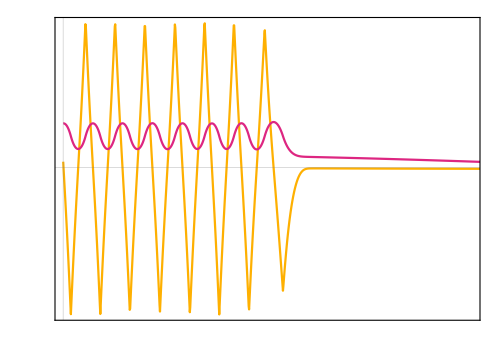

```mathematica
thetafncvals=Table[{r*(rscale*hbarGeV*clight)/10^3,thetafncin[r]},{r,0.001,67,0.01}];
thetaprimefncvals=Table[{r*(rscale*hbarGeV*clight)/10^3,thetafncinprime[r]},{r,0.001,67,0.01}];

Mag = 1.0;

xticks=Table[{j,If[Mod[j,10]==0,MaTeX[j,Magnification->Mag],None],If[Mod[j,10]==0,0.023,0.015]},{j,0,massradius[[1]]*10/10^3,5}];
xticksNV=Table[{j,If[Mod[j,10]==0,None,None],If[Mod[j,10]==0,0.023,0.015]},{j,0,massradius[[1]]*10/10^3,5}];
yticks=Table[{j,If[Mod[j,1]==0,MaTeX[j,Magnification->Mag],None],If[Mod[j,1]==0,0.023,0.015]},{j,-1,3,0.5}];
yticksNV=Table[{j,If[Mod[j,1]==0,None,None],If[Mod[j,1]==0,0.023,0.015]},{j,-1,3,0.5}];

ListPlot[{thetaprimefncvals,thetafncvals},PlotRange->{{0,20},All},Joined->True,PlotTheme->"Scientific",FrameTicks->{{yticks,yticksNV},{xticks,xticksNV}},FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}\\theta = \\frac{a}{2 f_a}",Magnification->2.0]},PlotStyle->{{c5,Thick},{c3,Thick},{c5,Thick},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}\\theta'",Magnification->2.0],MaTeX["\\color{darkgray}\\theta",Magnification->2.0]}]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/axion-field-vals-polytrope-2.pdf",%,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/axion-field-vals-polytrope-2.pdf

# Metric Perturbation Solver

```mathematica
Clear[densityinaxion]
```

### Solve for metric perturbations from axion

```mathematica
NSradiusscaled=r/.Normal[Solve[r*(rscale*hbarGeV*clight)/10^3 == massradius[[1]]/10^3,{r}][[1]]];

cfactor=GN*GeV2joules / (hbarGeV^3 * clight^7);
Vnat[rt_]:=-(1-densityfnc scaled[rt*rscale*hbarGeV*clight]*density coefficient sub)*4*masub^2*fasub^2*Abs[Cos[thetafnc[rt]]]*HeavisideTheta[NSradiusscaled - rt];
zetainhomogeneouspart[r_]:=(- Exp[λ[r]]*8*Pi*r*Vnat[r/(rscale*hbarGeV*clight)]*cfactor - (16*Pi*fasub^2/rscale^2)*r*thetafncprime[r/(rscale*hbarGeV*clight)]^2*cfactor)//.TOV replacements/.{M[r]->massfnc scaled[r]};
deltainhomogeneouspart[r_]:=(Exp[λ[r]]*8*Pi*r*Vnat[r/(rscale*hbarGeV*clight)]*cfactor - (16*Pi*fasub^2/rscale^2)*r*thetafncprime[r/(rscale*hbarGeV*clight)]^2*cfactor)//.TOV replacements/.{M[r]->massfnc scaled[r]};

massinaxion[r_,pg_]:=NIntegrate[4*Pi*rt^2*rscale^3*((thetafncprime[rt]*2*fasub/rscale)^2 + Vnat[rt]),{rt,0.001,r},Method->"GlobalAdaptive",PrecisionGoal->pg]*(GeV2joules/clight^2)*(GN/clight^2)

densityinaxion[r_]:=((thetafncprime[r]*2*fasub/rscale)^2 + Vnat[r])*(GeV2joules/clight^2)*(GN/clight^2)*(hbarGeV*clight)^(-3)

massinaxionfromdensity[r_,pg_]:=NIntegrate[4*Pi*rt^2*rscale^3*(hbarGeV*clight)^(3)*densityinaxion[rt],{rt,0.001,r},Method->"GlobalAdaptive",PrecisionGoal->pg]

zetaeq = (D[zeta[r],r] == Exp[λ[r]]*(1/r)*delta[r] - Exp[λ[r]]*8*Pi*r*Vnat[r/(rscale*hbarGeV*clight)]*cfactor - 8*Pi*fasub*r*thetafncprime[r/(rscale*hbarGeV*clight)]^2*cfactor)//.TOV replacements/.{M[r]->massfnc scaled[r]};
deltaeq = (D[delta[r],r] == Exp[λ[r]]*(-8*Pi*r*densityfnc scaled[r]*zeta[r]-(8*Pi*r*densityfnc scaled[r]+(1/r))*delta[r]) + Exp[λ[r]]*8*Pi*r*Vnat[r/(rscale*hbarGeV*clight)]*cfactor - 8*Pi*fasub*r*thetafncprime[r/(rscale*hbarGeV*clight)]^2*cfactor)//.TOV replacements/.{M[r]->massfnc scaled[r]};
```

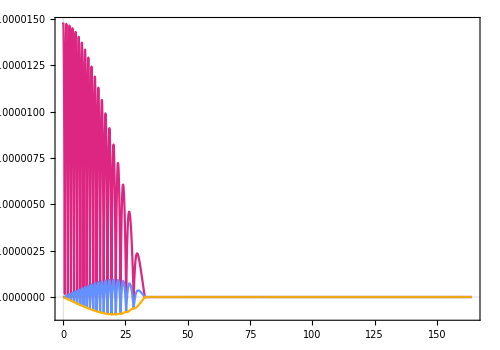

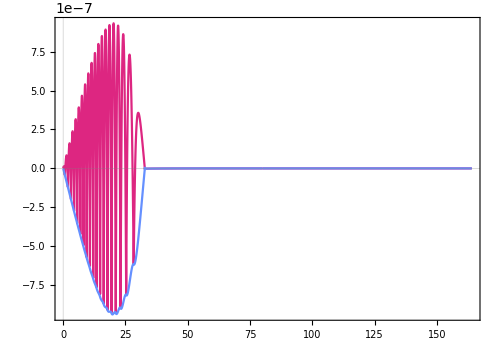

```mathematica
(* plot the axion potential *)
potentialvals=Table[{r/10^3,Vnat[r/(rscale*hbarGeV*clight)]},{r,10,massradius[[1]]*5,10}];
deltainhomogeneouspartvals=Table[{r/10^3,deltainhomogeneouspart[r]},{r,10,massradius[[1]]*5,10}];
zetainhomogeneouspartvals=Table[{r/10^3,zetainhomogeneouspart[r]},{r,10,massradius[[1]]*5,10}];

Mag = 1.0;

xticks=Table[{j,If[Mod[j,10]==0,MaTeX[j,Magnification->Mag],None],If[Mod[j,10]==0,0.023,0.015]},{j,0,massradius[[1]]*10/10^3,5}];
xticksNV=Table[{j,If[Mod[j,10]==0,None,None],If[Mod[j,10]==0,0.023,0.015]},{j,0,massradius[[1]]*10/10^3,5}];
yticks=Table[{j,If[Mod[j,0.1]==0,MaTeX[j,Magnification->Mag],None],If[Mod[j,0.1]==0,0.023,0.015]},{j,-1,0.0,0.1}];
yticksNV=Table[{j,If[Mod[j,0.1]==0,None,None],If[Mod[j,0.1]==0,0.023,0.015]},{j,-1,0.0,0.1}];

potentialplot = ListPlot[{potentialvals,deltainhomogeneouspartvals,zetainhomogeneouspartvals},PlotRange->All,Joined->True,PlotTheme->"Scientific",FrameTicks->(*{{yticks,yticksNV},{xticks,xticksNV}}*)Automatic,FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}V(r) \\ \\left[\\text{m}^{-2} \\right]",Magnification->2.0]},PlotStyle->{{c3,Thick},{c1,Thick},{c5,Thick},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}V(r)",Magnification->1.5],MaTeX["\\color{darkgray}\\delta(r)",Magnification->1.5],MaTeX["\\color{darkgray}\\zeta(r)",Magnification->1.5]}]

inhomogeneousplot = ListPlot[{deltainhomogeneouspartvals,zetainhomogeneouspartvals},PlotRange->All,Joined->True,PlotTheme->"Scientific",FrameTicks->(*{{yticks,yticksNV},{xticks,xticksNV}}*)Automatic,FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}V(r) \\ \\left[\\text{m}^{-2} \\right]",Magnification->2.0]},PlotStyle->{{c3,Thick},{c1,Thick},{c5,Dashed},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}\\delta(r)",Magnification->1.5],MaTeX["\\color{darkgray}\\zeta(r)",Magnification->1.5]}]
```

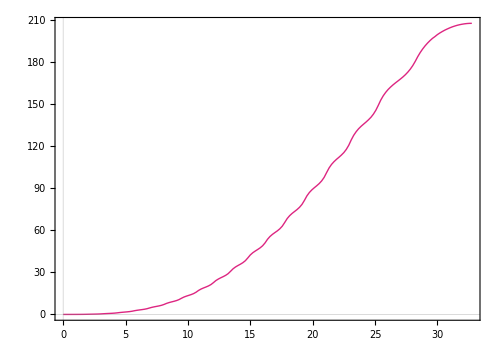

```mathematica
axionfieldmassvals=Table[{r*rscale*hbarGeV*clight/10^3,massinaxion[r,4]},{r,0.001,NSradiusscaled,0.1}];

massinaxionplot = ListPlot[{axionfieldmassvals},PlotRange->All,Joined->True,PlotTheme->"Scientific",FrameTicks->(*{{yticks,yticksNV},{xticks,xticksNV}}*)Automatic,FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}M_a(r) \\ \\left[\\text{m} \\right]",Magnification->2.0]},PlotStyle->{{c3,Thick},{c1,Thick},{c5,Dashed},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/mass-in-axion-field.pdf",massinaxionplot,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/mass-in-axion-field.pdf

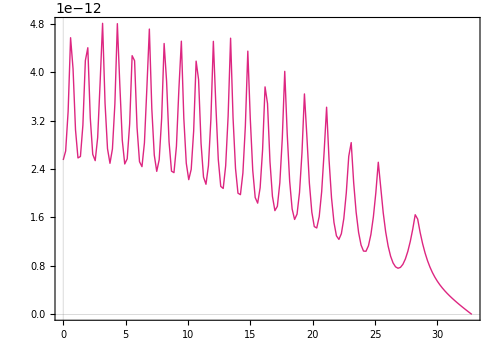

```mathematica
axionfielddensityvals=Table[{r*rscale*hbarGeV*clight/10^3,densityinaxion[r]},{r,0.001,NSradiusscaled,0.1}];

densityinaxionplot = ListPlot[{axionfielddensityvals},PlotRange->All,Joined->True,PlotTheme->"Scientific",FrameTicks->(*{{yticks,yticksNV},{xticks,xticksNV}}*)Automatic,FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}\\rho_a(r) \\ \\left[\\text{m}^{-2} \\right]",Magnification->2.0]},PlotStyle->{{c3,Thick},{c1,Thick},{c5,Dashed},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/density-in-axion-field.pdf",densityinaxionplot,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/axions-in-NS/figures/density-in-axion-field.pdf

```mathematica
totalmassinaxioninNS = massinaxion[NSradiusscaled,8]
totalmassinaxioninNSfromdensity = massinaxionfromdensity[NSradiusscaled,8]
massNSinmeters=sols[[1]][[2]]/Sqrt[ρscale]
```

207.894

207.894

4418.72

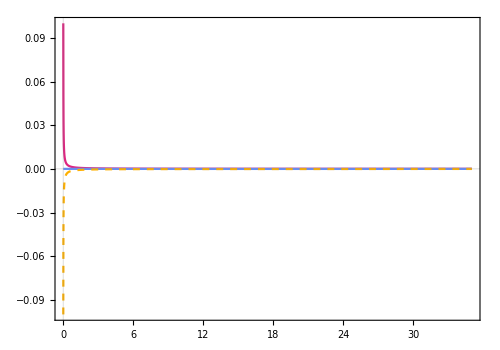

```mathematica
M12=Table[{r/10^3,Exp[λ[r]]*(1/r)//.TOV replacements/.{M[r]->massfnc scaled[r]}},{r,10,35*10^3,10}];
M21=Table[{r/10^3,Exp[λ[r]]*(-8*Pi*r*densityfnc scaled[r]) //.TOV replacements/.{M[r]->massfnc scaled[r]}},{r,10,35*10^3,10}];
M22=Table[{r/10^3,Exp[λ[r]]*(-(8*Pi*r*densityfnc scaled[r]+(1/r))) //.TOV replacements/.{M[r]->massfnc scaled[r]}},{r,10,35*10^3,10}];

ListPlot[{M12,M21,M22},PlotRange->All,Joined->True,PlotTheme->"Scientific",FrameTicks->(*{{yticks,yticksNV},{xticks,xticksNV}}*)Automatic,FrameLabel->{MaTeX["\\color{darkgray}r \\ \\left[\\text{km} \\right]",Magnification->2.0],MaTeX["\\color{darkgray}V(r) \\ \\left[\\text{m}^{-2} \\right]",Magnification->2.0]},PlotStyle->{{c3,Thick},{c1,Thick},{c5,Dashed},{c2,Dashed,Thick}},ImageSize->{500,350},AspectRatio->Full,PlotLegends->{MaTeX["\\color{darkgray}M_{12}",Magnification->1.5],MaTeX["\\color{darkgray}M_{21}",Magnification->1.5],MaTeX["\\color{darkgray}M_{22}",Magnification->1.5]}]
```

```mathematica
(* set boundary conditions on perturbations so that they match at the NS radius *)
ζbc = (-2*totalmassinaxioninNS/massradius[[1]])/gtt[massradius[[1]]]
Δbc = (-2*totalmassinaxioninNS/(massradius[[1]]*(1-2*massNSinmeters/massradius[[1]])^2))/grr[massradius[[1]]]
```

-0.0173588

0.0173588

```mathematica
ζout[r_]:= (-2*totalmassinaxioninNS/r)/gtt[r]
Δout[r_]:= (-2*totalmassinaxioninNS/(r*(1-2*massNSinmeters/r)^2))/grr[r]
```

```mathematica
myperturbationsols=NDSolve[{zetaeq,deltaeq,zeta[massradius[[1]]]==ζbc,delta[massradius[[1]]]==Δbc},{zeta, delta},{r,10,massradius[[1]]},PrecisionGoal->4][[1]];
zetafnc[r_]:=Evaluate[zeta[r]/.myperturbationsols]
deltafnc[r_]:=Evaluate[delta[r]/.myperturbationsols]
```

```mathematica
massradius[[1]]
```

32790.

# Solve Axion EOM in constant density NS

```mathematica
constant density replacements bigr={ρ0->4.31013*10^8 ,
σN->59,
mp->135.0,
fp->130.0,
ϵ->0.001,
rsp->2.5,
mT ->(mp*fp/(2*fa))*Sqrt[σN*nN/(mp^2*fp^2) - ϵ],
mn->939.565,
nN->ρ0/mn,
fa->10^16*10^3,
ma->mp*fp*Sqrt[ϵ]/(2*fa),
G->6.70883*10^(-45)};
constant density replacements smallr={ρ0->4.31013*10^8 ,
σN->59,
mp->135.0,
fp->130.0,
ϵ->0.001,
rsp->0.005,
mT ->(mp*fp/(2*fa))*Sqrt[σN*nN/(mp^2*fp^2) - ϵ],
mn->939.565,
nN->ρ0/mn,
fa->10^16*10^3,
ma->mp*fp*Sqrt[ϵ]/(2*fa),
G->6.70883*10^(-45)};
```

```mathematica
(ma^2/mT^2)//.constant density replacements bigr
(ma^2/mT^2)//.constant density replacements smallr
```

0.0115109

0.0115109

```mathematica
fa//.constant density replacements smallr
```

10000000000000000000

```mathematica
mass cd[r_]:=ρ0*(4/3)*Pi*r^3
elambda[r_]:=1/(1 - 2*G*mass cd[r]/r)
```

#### Solve in r coordinate

```mathematica
eq1 = (-(1/2)*(1/elambda[rp/mT])*theta''[rp]==-(1 -HeavisideTheta[r-rs]*(1 + ma^2/mT^2)) * Sin[theta[rp]/2]*Sign[Cos[theta[rp]/2]])//.constant density replacements;
(*eq2 = (D[axion[r],r]==f[r])//.constant density replacements;*)
ic1= (theta[rs]==1.0)//.constant density replacements;
ic2= (theta'[rs]==0.01)//.constant density replacements;
```

```mathematica
eq1
ic1
ic2
```

-1/2 (1-0.000403988 rp^2) theta''(rp)==(1.12841 r-1.8-1) sin((theta(rp))/2) cos((theta(rp))/2)

theta(18.)==0.

theta'(18.)==0.

```mathematica
sol=NDSolve[{eq1,ic1,ic2},theta,{rp,0.0,5}]
```

NDSolve[{-1/2 (1-0.000403988 rp^2) theta''(rp)==(1.12841 r-2.5-1) sin((theta(rp))/2) cos((theta(rp))/2),theta(2.5)==1.,theta'(2.5)==0.01},theta,{rp,0.,5}]

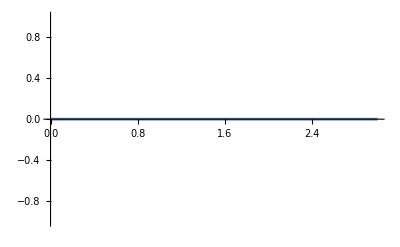

```mathematica
Plot[Evaluate[theta[r]/. sol],{r,0,3},PlotStyle->Automatic]
```

#### Tan(x) coordinates

```mathematica
ArcTan[rsp]//.constant density replacements bigr
ArcTan[rsp]//.constant density replacements smallr
```

1.19029

0.00499996

```mathematica
Clear[eq1,ic1,ic2]
eq1 = (-(1/2)*(1/elambda[Tan[x]/mT])*(-2*Cos[x]*Sin[x]*theta'[x]+Cos[x]^2 * theta''[x])==-(1 -HeavisideTheta[Tan[x] - rsp]*(1 + ma^2/mT^2)) * Sin[theta[x]/2]*Sign[Cos[theta[x]/2]])//.constant density replacements bigr;
(*eq2 = (D[axion[r],r]==f[r])//.constant density replacements;*)
ic1= (theta[Pi/2]==1.0)//.constant density replacements bigr;
ic2= (theta'[Pi/2]==0.0)//.constant density replacements bigr;
```

```mathematica
solbigr=NDSolve[{eq1,ic1,ic2},theta,{x,0.0,Pi/2},Method->{"EquationSimplification"->"Solve"}]
```

{{theta→InterpolatingFunction[…]}}

```mathematica
Clear[eq1,ic1,ic2]
eq1 = (-(1/2)*(1/elambda[Tan[x]/mT])*(-2*Cos[x]*Sin[x]*theta'[x]+Cos[x]^2 * theta''[x])==-(1 -HeavisideTheta[Tan[x] - rsp]*(1 + ma^2/mT^2)) * Sin[theta[x]/2]*Sign[Cos[theta[x]/2]])//.constant density replacements smallr;
(*eq2 = (D[axion[r],r]==f[r])//.constant density replacements;*)
ic1= (theta[Pi/2]==1.0)//.constant density replacements smallr;
ic2= (theta'[Pi/2]==0.0)//.constant density replacements smallr;
```

```mathematica
solsmallr=NDSolve[{eq1,ic1,ic2},theta,{x,0.0,Pi/2},Method->{"EquationSimplification"->"Solve"}]
```

{{theta→InterpolatingFunction[…]}}

```mathematica
theta[0]/. solbigr[[1]]
```

38.601

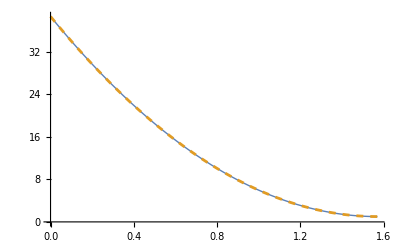

```mathematica
Plot[{Evaluate[theta[x]/. solbigr],Evaluate[theta[x]/. solsmallr]},{x,0,Pi/2},PlotStyle->{Thick,Dashed}]
```

#### Plot as a function of r not of x

```mathematica
axionthetavalsbigr=Table[{Tan[x],theta[x]/.solbigr[[1]]},{x,ArcTan[0.0],ArcTan[10.0],0.01}];
axionthetavalssmallr=Table[{Tan[x],theta[x]/.solsmallr[[1]]},{x,ArcTan[0.0],ArcTan[10.0],0.01}];
```

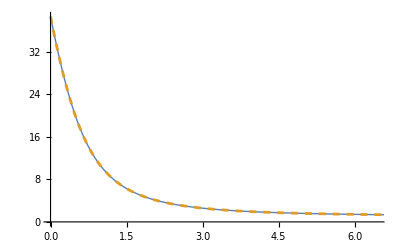

```mathematica
ListPlot[{axionthetavalsbigr,axionthetavalssmallr},Joined->True,PlotStyle->{Thick,Dashed}]
```

I’m not seeing the phase transition in r that I’m expecting to see. I also get much larger values at the center than the Hook paper.

```mathematica
axionthetavalsbigr=Table[{Tan[x],theta''[x]/.solbigr[[1]]},{x,ArcTan[0.0],ArcTan[10.0],0.01}];
axionthetavalssmallr=Table[{Tan[x],theta''[x]/.solsmallr[[1]]},{x,ArcTan[0.0],ArcTan[10.0],0.01}];
```

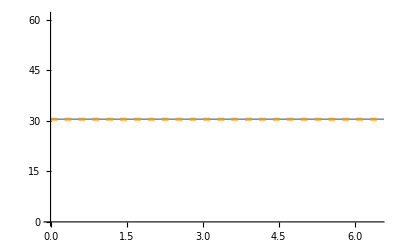

```mathematica
ListPlot[{axionthetavalsbigr,axionthetavalssmallr},Joined->True,PlotStyle->{Thick,Dashed}]
```

And this is an obvious problem I would think. The double derivative should change at rsp I would have thought.

```mathematica
LHSVals=Table[{x,(-(1/2)*(1/elambda[Tan[x]/mT])*(-2*Cos[x]*Sin[x]*theta'[x]+Cos[x]^2 * theta''[x]))/.solbigr[[1]]//.constant density replacements bigr},{x,0,Pi/2,0.01}];
RHSVals=Table[{x,(-(1 -HeavisideTheta[Tan[x] - rsp]*(1 + ma^2/mT^2)) * Sin[theta[x]/2]*Sign[Cos[theta[x]/2]])/.solbigr[[1]]//.constant density replacements bigr},{x,0,Pi/2,0.01}];
```

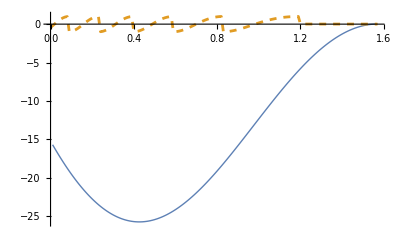

```mathematica
ListPlot[{LHSVals,RHSVals},Joined->True,PlotStyle->{Thick,Dashed}]
```

```mathematica
rsp//.constant density replacements smallr
```

0.005

Okay yeah there’s a problem here. I’m not sure why the Heaviside function isn’t working, but it isn’t.

I have no idea where the saw tooth is coming from.

# Deprecated

Integrating from 0 to r gives Exp[-λ(r)] = 1 - 2*(m(r) + ρ_a(r))/r since we need to get a flat metric back at large r. This is the result we’d expect naively. Set these replacements below.

```mathematica
ρareplacement={ρa[r]->Taud[[1,1]]};
λreplacements={Exp[λ[r]]->1/(-2*(m[r]+Ea[r])/r+1),Exp[-λ[r]]->-2*(m[r]+Ea[r])/r+1};
```

```mathematica
eq22=Einstein[[2,2]]==8*Pi*Ttdd[[2,2]](*/.λreplacements*)//FullSimplify
```

((8 π r^2 p(r)+1) ⅇ^(λ(r)))/r==4 π r ((a'(r))^2+2 ⅇ^(λ(r)) Va(r))+ν'(r)+1/r

Everything up to this point is the same as we’d get for the standard TOV. The problem comes in when we ask which T we should set to be divergenceless.

```mathematica
(* check that Taxion is divergence free *)
divTaxionud =covariant[Taud,{up,down}];
divTaxionud = Table[Simplify[Sum[divTaxionud[[i,i,k]],{i,1,4}]],{k,1,4}]//Simplify
```

{0,(ⅇ^(-λ(r)) (a'(r))^2 (-r λ'(r)+r ν'(r)+4))/(2 r)+ⅇ^(-λ(r)) a'(r) a''(r)+Va'(r),0,0}

I think maybe we can see a ρ_a'(r) in there somewhere in the last two terms.

```mathematica
divTNSud =covariant[TNSud,{up,down}];
divTNSud = Table[Simplify[Sum[divTNSud[[i,i,k]],{i,1,4}]],{k,1,4}]
```

{0,-p'(r)-1/2 (p(r)+ρ(r)) ν'(r),0,0}

What we really want is to be able to write the axion piece the same way as the baryonic piece. Let’s just check if that’s true.

```mathematica
(-D[Taud[[2,2]],r] - (1/2)*(Taud[[1,1]]+Taud[[2,2]])*ν'[r]-divTaxionud[[2]])//Simplify
```

(ⅇ^(-λ(r)) (a'(r))^2 (2 r λ'(r)-r ν'(r)-4))/(2 r)-2 ⅇ^(-λ(r)) a'(r) a''(r)-2 Va'(r)-Va(r) ν'(r)

It doesn’t totally work out that way which is frustrating. But I think it makes sense.

```mathematica
divTaxionud[[2]]//Simplify
```

(ⅇ^(-λ(r)) (a'(r))^2 (-r λ'(r)+r ν'(r)+4))/(2 r)+ⅇ^(-λ(r)) a'(r) a''(r)+Va'(r)

```mathematica
Taud
```

(Va(r)-1/2 ⅇ^(-λ(r)) (a'(r))^2 | 0 | 0 | 0
0 | 1/2 ⅇ^(-λ(r)) (a'(r))^2+Va(r) | 0 | 0
0 | 0 | Va(r)-1/2 ⅇ^(-λ(r)) (a'(r))^2 | 0
0 | 0 | 0 | Va(r)-1/2 ⅇ^(-λ(r)) (a'(r))^2)

```mathematica
(* divergence of axion T is not zero on its own. Is that a problem? *)
```

```mathematica
(* enforce that TNS is divergence free *)
divTtud =covariant[Ttud,{up,down}];
divTtud = Table[Simplify[Sum[divTtud[[i,i,k]],{i,1,4}]],{k,1,4}]
```

{0,(ⅇ^(-λ(r)) ((a'(r))^2 (-r λ'(r)+r ν'(r)+4)+2 r a'(r) a''(r)-r ⅇ^(λ(r)) (2 p'(r)+(p(r)+ρ(r)) ν'(r)-2 Va'(r))))/(2 r),0,0}

```mathematica
divTtr=FullSimplify[divTtud[[2]]]
```

(ⅇ^(-λ(r)) ((a'(r))^2 (-r λ'(r)+r ν'(r)+4)+2 r a'(r) a''(r)-r ⅇ^(λ(r)) (2 p'(r)+(p(r)+ρ(r)) ν'(r)-2 Va'(r))))/(2 r)

```mathematica
νreplacement=Solve[divTtr==0,ν'[r]][[1]]
```

{ν'(r)→(-r (a'(r))^2 λ'(r)+4 (a'(r))^2+2 r a'(r) a''(r)-2 r ⅇ^(λ(r)) p'(r)+2 r ⅇ^(λ(r)) Va'(r))/(r (-(a'(r))^2+p(r) ⅇ^(λ(r))+ⅇ^(λ(r)) ρ(r)))}

```mathematica
TOVwithAxion=eq22/.νreplacement(*/.λreplacements*)
```

((8 π r^2 p(r)+1) ⅇ^(λ(r)))/r==4 π r ((a'(r))^2+2 ⅇ^(λ(r)) Va(r))+(-r (a'(r))^2 λ'(r)+4 (a'(r))^2+2 r a'(r) a''(r)-2 r ⅇ^(λ(r)) p'(r)+2 r ⅇ^(λ(r)) Va'(r))/(r (-(a'(r))^2+p(r) ⅇ^(λ(r))+ⅇ^(λ(r)) ρ(r)))+1/r

```mathematica
TOVwithAxion=FullSimplify[TOVwithAxion]
```

(-4 π r^2 ((a'(r))^2+2 ⅇ^(λ(r)) Va(r))+((a'(r))^2 (r λ'(r)-4)-2 r a'(r) a''(r)+2 r ⅇ^(λ(r)) (p'(r)-Va'(r)))/(ⅇ^(λ(r)) (p(r)+ρ(r))-(a'(r))^2)+(8 π r^2 p(r)+1) ⅇ^(λ(r))-1)/r==0

```mathematica
eqrhoprime=ρa'[r]==D[Taud[[1,1]],r]//Simplify
eqpprime=pa'[r]==D[Taud[[2,2]],r]//Simplify
```

ρa'(r)==1/2 ⅇ^(-λ(r)) a'(r) (a'(r) λ'(r)-2 a''(r))+Va'(r)

1/2 ⅇ^(-λ(r)) a'(r) (a'(r) λ'(r)-2 a''(r))+pa'(r)==Va'(r)

```mathematica
Taud[[1,1]]
Taud[[2,2]]
```

Va(r)-1/2 ⅇ^(-λ(r)) (a'(r))^2

1/2 ⅇ^(-λ(r)) (a'(r))^2+Va(r)

# Misc

```mathematica
(2*(3*r^2 + 2*(Mfnc[r]^2 + Pi*r^4*(pfnc[r]*(-9 + 16*Pi*r^2*pfnc[r]) - 5*ρfnc[r]) + r*Mfnc[r]*(-3 + 2*Pi*r^2*(13*pfnc[r] + 5*ρfnc[r])) + (Pi*r^4*(r - 2*Mfnc[r])^2*ρprimefnc[r])/(Mfnc[r] + 4*Pi*r^3*pfnc[r]))))/(r*(r - 2*Mfnc[r])) == ((2*y[r]*(r - Mfnc[r] + 2*Pi*r^3*(pfnc[r] - ρfnc[r])) + r*(r - 2*Mfnc[r])*(y[r]^2/Rstar + Derivative[1][y][r])))/Rstar
```

(2 (3 r^2+2 (Mfnc[r]^2+π r^4 (pfnc[r] (-9+16 π r^2 pfnc[r])-5 ρfnc[r])+r Mfnc[r] (-3+2 π r^2 (13 pfnc[r]+5 ρfnc[r]))+(π r^4 (r-2 Mfnc[r])^2 ρprimefnc[r])/(Mfnc[r]+4 π r^3 pfnc[r]))))/(r (r-2 Mfnc[r]))==(2 y[r] (r-Mfnc[r]+2 π r^3 (pfnc[r]-ρfnc[r]))+r (r-2 Mfnc[r]) (y[r]^2/Rstar+y'[r]))/Rstar

```mathematica
%//TraditionalForm
```

(2 (2 (r Mfnc(r) (2 π r^2 (13 pfnc(r)+5 ρfnc(r))-3)+(π r^4 (r-2 Mfnc(r))^2 ρprimefnc(r))/(Mfnc(r)+4 π r^3 pfnc(r))+(Mfnc(r))^2+π r^4 (pfnc(r) (16 π r^2 pfnc(r)-9)-5 ρfnc(r)))+3 r^2))/(r (r-2 Mfnc(r)))==(2 y(r) (-Mfnc(r)+2 π r^3 (pfnc(r)-ρfnc(r))+r)+r (r-2 Mfnc(r)) ((y(r))^2/Rstar+y'(r)))/Rstar

### Initial conditions on axion at center of star

```mathematica
Mstart = 4*Pi*r^3*ρ0/2;
Mpstart =4*Pi*r^2*ρ0;
pstart=p0-2*Pi*(p0+ρ0)*(ρ0/3+p0)*r^2;
θstart = θ0+θ1*r+θ2*r^2;
θpstart = θ1+2*θ2*r;
θppstart =2*θ2;
```

```mathematica
((-2*ma^2 + (ρ0*σ)/(fa^2*mn))*Sin[θ0])/8
```

```mathematica
thetareplacements = {θ1->0,θ2->-Sin[θ0]*(2*ma^2-ρ0*σ/(fa^2*mn))/(8)};
```

```mathematica
EOMstartLHS = -((1 - 2*Mstart/r)*θppstart + (2*(Mstart +2*Pi*r^3*(ρ0-pstart)-r)/r^2)*θpstart)/.thetareplacements;
EOMstartRHS = ((ma^2/2 - σ*ρ0/(4*mn*fa^2))*(Sin[θstart]*Cos[θstart]/RealAbs[Cos[θstart]] + θpstart*(8*Cos[2*θstart]*Cos[θstart]^2 - Cos[4*θstart]+1)/(8*RealAbs[Cos[θstart]]^3)*r))/.thetareplacements;
```

```mathematica
LHSseries = Normal[Series[EOMstartLHS,{r,0,0}]]//Simplify
RHSseries = Normal[Series[EOMstartRHS,{r,0,0},Assumptions->{Element[r|θ1|θ2,Reals],θ0>Pi/2,ρ0>0,σ>0,mn>0}]]//Simplify
```

2 θ2

Piecewise[{{1/4 (-2 ma^2+(ρ0 σ)/(fa^2 mn)) Sin[θ0], Cos[θ0+r^2 θ2]<0}, {1/4 (2 ma^2-(ρ0 σ)/(fa^2 mn)) Sin[θ0], True}}]

```mathematica
RHSseries[[1]][[1]][[1]]
```

1/4 (-2 ma^2+(ρ0 σ)/(fa^2 mn)) Sin[θ0]

```mathematica
Solve[RHSseries[[1]][[1]][[1]]==LHSseries,θ2]
```

{{θ2→-((2 fa^2 ma^2 mn-ρ0 σ) Sin[θ0])/(8 fa^2 mn)}}

```mathematica
Solve[RHSseries[[2]]==LHSseries,θ0]
```

{{θ0→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{θ0→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]},{θ0→ConditionalExpression[ArcTan[(32 fa^2 mn π (p0-ρ0))/(3 (2 fa^2 ma^2 mn-ρ0 σ)),-(√(36 fa^4 ma^4 mn^2-1024 fa^4 mn^2 p0^2 π^2+2048 fa^4 mn^2 p0 π^2 ρ0-1024 fa^4 mn^2 π^2 ρ0^2-36 fa^2 ma^2 mn ρ0 σ+9 ρ0^2 σ^2))/(√(36 fa^4 ma^4 mn^2-36 fa^2 ma^2 mn ρ0 σ+9 ρ0^2 σ^2))]+2 π C[1], C[1]∈ℤ]},{θ0→ConditionalExpression[ArcTan[(32 fa^2 mn π (p0-ρ0))/(3 (2 fa^2 ma^2 mn-ρ0 σ)),(√(36 fa^4 ma^4 mn^2-1024 fa^4 mn^2 p0^2 π^2+2048 fa^4 mn^2 p0 π^2 ρ0-1024 fa^4 mn^2 π^2 ρ0^2-36 fa^2 ma^2 mn ρ0 σ+9 ρ0^2 σ^2))/(√(36 fa^4 ma^4 mn^2-36 fa^2 ma^2 mn ρ0 σ+9 ρ0^2 σ^2))]+2 π C[1], C[1]∈ℤ]}}

```mathematica
θ2/.%[[1]]
```

-((2 fa^2 ma^2 mn-ρ0 σ) Sin[θ0])/(8 fa^2 mn)

```mathematica
Normal[%]/.{C[1]->0}
```

ArcTan[-(32 fa^2 mn π (p0-ρ0))/(3 (2 fa^2 ma^2 mn-ρ0 σ)),-(√(36 fa^4 ma^4 mn^2-1024 fa^4 mn^2 p0^2 π^2+2048 fa^4 mn^2 p0 π^2 ρ0-1024 fa^4 mn^2 π^2 ρ0^2-36 fa^2 ma^2 mn ρ0 σ+9 ρ0^2 σ^2))/(√(36 fa^4 ma^4 mn^2-36 fa^2 ma^2 mn ρ0 σ+9 ρ0^2 σ^2))]

```mathematica
Simplify[%]
```

1/8 (-2 ma^2+(ρ0 σ)/(fa^2 mn)) Sin[θ0]

```mathematica
FullSimplify[%]
```

ArcTan[(32 fa^2 mn π (p0-ρ0))/(-2 fa^2 ma^2 mn+ρ0 σ),-(√(4 fa^4 mn^2 (9 ma^4-256 π^2 (p0-ρ0)^2)-36 fa^2 ma^2 mn ρ0 σ+9 ρ0^2 σ^2))/(√((-2 fa^2 ma^2 mn+ρ0 σ)^2))]

```mathematica
%//InputForm
```

((-2*ma^2 + (ρ0*σ)/(fa^2*mn))*Sin[θ0])/8

```mathematica
Solve[2*θ2==-(Sin[θ0]*(2*fa^2*ma^2*mn-ρ0*σ)/(4*fa^2*mn))*(Cos[θ0+θ2*r^2]/RealAbs[Cos[θ0+θ2*r^2]]),θ2]
```

$Aborted

```mathematica
%[[1]]//InputForm
```

{θ1 -> (Sqrt[2]*fa^2*mn*θ2)/(ρ0*σ)}

```mathematica
θ00000=ArcTan[-(32*fa^2*mn*Pi*(p0-ρ0)),-(Sqrt[4*fa^4*mn^2*(9*ma^4-256*Pi^2*(p0-ρ0)^2)-36*fa^2*ma^2*mn*ρ0*σ+9*ρ0^2*σ^2])]
```

ArcTan[-32 fa^2 mn π (p0-ρ0),-√(4 fa^4 mn^2 (9 ma^4-256 π^2 (p0-ρ0)^2)-36 fa^2 ma^2 mn ρ0 σ+9 ρ0^2 σ^2)]

```mathematica
FullSimplify[θ00000]
```

ArcTan[32 fa^2 mn π (-p0+ρ0),-√(4 fa^4 mn^2 (9 ma^4-256 π^2 (p0-ρ0)^2)-36 fa^2 ma^2 mn ρ0 σ+9 ρ0^2 σ^2)]

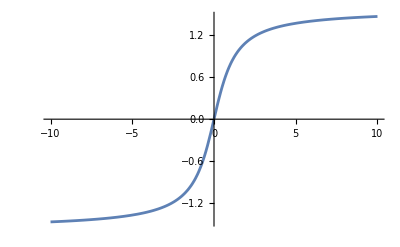

```mathematica
Plot[ArcTan[x],{x,-10,10}]
```